```mathematica
Quit[]
```

# Esoptrogenesis

## A model for the dark matter-baryon coincidence.

## Preamble

## Directories

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/mbuenabad/Dropbox/Projects/Active/a1_baryon_dm_coincidence/mathematica files

```mathematica
PlotsDir=NotebookDirectory[]<>"../plots/"
```

/home/mbuenabad/Dropbox/Projects/Active/a1_baryon_dm_coincidence/mathematica files/../plots/

## Packages

### InterpolatingFunctionsAnatomy

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
```

### FixPoligons

```mathematica
<<FixPolygons`
```

### MaTeX

```mathematica
<<MaTeX`

SetOptions[MaTeX,"Preamble"->{"\\usepackage{amssymb,amsmath,latexsym,amsfonts,amsthm,color}"}];
SetOptions[MaTeX,"Preamble"->{"\\usepackage{slashed}","\\usepackage{color}","\\definecolor{purplev}{rgb}{0.5, 0, 0.5}","\\definecolor{bluearrow}{rgb}{0.12, 0.56, 1}","\\definecolor{redarrow}{rgb}{1, 0.39, 0.28}","\\definecolor{greenarrow}{rgb}{0.0941,0.545,0.133}"}];
```

## Other Plotting Utilities

### Custom Ticks

```mathematica
Clear[FloatToInt,LinTicks,LinTicksNoLabels,LinTicksAllLabels,PrettyExp,PrettySciNot,LogTicks,LogTicksNoLabels,LogTicksAllLabels,myTickStyle]
```

```mathematica
FloatToInt[x_]:=If[IntegerPart[x]==x,IntegerPart[x],x]
```

#### Linear

```mathematica
LinTicks[min_,max_,sz_:1,step_:1/2]:=DeleteDuplicates[Table[{x,MaTeX[ToString[FloatToInt[x]],Magnification->sz],{.025,0}},{x,min,max}]~Join~Table[{x,Null,{0.01,0}},{x,min,max,step}],#1⟦1⟧==#2⟦1⟧&]

LinTicksNoLabels[min_,max_,step_:1/2]:=Table[{x,Null,{If[IntegerQ[x],.025,0.01],0}},{x,min,max,step}]

LinTicksAllLabels[min_,max_,sz_:1,step_:1/2]:=DeleteDuplicates[Table[{x,MaTeX[ToString[FloatToInt[x//N]],Magnification->sz],{.025,0}},{x,min,max}]~Join~Table[{x,MaTeX[ToString[FloatToInt[x//N]],Magnification->sz],{0.01,0}},{x,min,max,step}],#1⟦1⟧==#2⟦1⟧&]
```

#### Logarithmic

```mathematica
PrettyExp[x_,MAX_:2,sz_:1]:=If[Abs[x]≥MAX,MaTeX["10^{"<>ToString[x]<>"}",Magnification->sz],If[x≥0,MaTeX[ToString[10^x],Magnification->sz],MaTeX[ToString[10.^x],Magnification->sz]]]

PrettySciNot[y_,x_,MAX_:2,sz_:1]:=If[Abs[x]≥MAX,MaTeX[ToString[y]<>"\\times 10^{"<>ToString[x]<>"}",Magnification->sz],If[x≥0,MaTeX[ToString[y*10^x],Magnification->sz],MaTeX[ToString[y*10.^x],Magnification->sz]]]
```

```mathematica
LogTicks[min_,max_,AMAX_:2,sz_:1,useLog_:False]:=Flatten[Table[Prepend[Flatten[Table[{(*i*10.^x*)If[useLog,Log10[i]+x,i*10.^x],"",{0.01,0}},{i,2,9}],{1}],{(*10.^x*)If[useLog,x,10.^x],PrettyExp[x,AMAX,sz],{.025,0}}],{x,Floor[Log[10,min]],Ceiling[Log[10,max]],1}],1]

LogTicksNoLabels[min_,max_,useLog_:False]:=Flatten[Table[Prepend[Flatten[Table[{(*i*10.^x*)If[useLog,Log10[i]+x,i*10.^x],"",{0.01,0}},{i,2,9}],{1}],{(*10.^x*)If[useLog,x,10.^x],"",{.025,0}}],{x,Floor[Log[10,min]],Ceiling[Log[10,max]],1}],1]

LogTicksAllLabels[min_,max_,AMAX_:2,sz_:1,useLog_:False]:=Flatten[Table[Prepend[Flatten[Table[{(*i*10.^x*)If[useLog,Log10[i]+x,i*10.^x],PrettySciNot[i,x,AMAX,sz],{0.01,0}},{i,2,9}],{1}],{(*10.^x*)If[useLog,x,10.^x],PrettyExp[x,AMAX,sz],{.025,0}}],{x,Floor[Log[10,min]],Ceiling[Log[10,max]],1}],1]
```

#### Tick Style

```mathematica
myTickStyle[col_,sz_]:=Directive[col,sz]
```

#### (*Old*)

```mathematica
(*Clear[myLinTicks,myLogTicks]*)
```

```mathematica
(*myLinTicks[sz_,xLims_:{-10,10},yLims_:{-10,10}]:=Block[{xTicks,yTicks,res},

xTicks={DeleteDuplicates[Table[{x,MaTeX[ToString[x],Magnification->sz],{0,-0.015}},{x,xLims⟦1⟧,xLims⟦2⟧}]~Join~Table[{x,Null,{0,-0.0075}},{x,xLims⟦1⟧,xLims⟦2⟧,1/2}],#1⟦1⟧==#2⟦1⟧&],Table[{x,Null,{0,If[IntegerQ[x],-0.015,-0.0075]}},{x,xLims⟦1⟧,xLims⟦2⟧,1/2}]};
yTicks={DeleteDuplicates[Table[{y,MaTeX[ToString[y],Magnification->sz],{0,-0.015}},{y,yLims⟦1⟧,yLims⟦2⟧}]~Join~Table[{y,Null,{0,-0.0075}},{y,yLims⟦1⟧,yLims⟦2⟧,1/2}],#1⟦1⟧==#2⟦1⟧&],Table[{y,Null,{0,If[IntegerQ[y],-0.015,-0.0075]}},{y,yLims⟦1⟧,yLims⟦2⟧,1/2}]};

res={xTicks,yTicks};

res
]

myLogTicks[LXs_,LYs_,Unlabel_:True,LabelXAllTicks_:False]:=Block[{xBottomLabel,xBottomUnLabel,xTopUnLabel,xBottom,xTop,yLeftLabel,yLeftUnLabel,yRightUnLabel,yLeft,yRight,res},

If[LabelXAllTicks,
xBottomLabel=Table[{i,If[-1<i<2,10^i,Superscript[10,i]]},{i,LXs⟦1⟧,LXs⟦2⟧}];
xBottomLabel=xBottomLabel~Join~Flatten[Table[{Log10[k*j]//N,(k*j)//N},{k,2,9},{j,10^xBottomLabel⟦All,1⟧}],1];
xBottomUnLabel={};
xTopUnLabel=Table[{i,Null},{i,LXs⟦1⟧,LXs⟦2⟧}];
xTopUnLabel=xTopUnLabel~Join~Flatten[Table[{Log10[k*j]//N,Null},{k,2,9},{j,10^xTopUnLabel⟦All,1⟧}],1];
,
xBottomLabel=Table[{i,If[-1<i<2,10^i,Superscript[10,i]]},{i,LXs⟦1⟧,LXs⟦2⟧}];
xBottomUnLabel=Flatten[Table[{Log10[k*j]//N,Null},{k,2,9},{j,10^xBottomLabel⟦All,1⟧}],1];
xTopUnLabel=Flatten[Table[{Log10[k*j]//N,Null},{k,1,9},{j,10^xBottomLabel⟦All,1⟧}],1];
];
(*xBottomLabel=Table[{i,If[-1<i<2,10^i,Superscript[10,i]]},{i,LXs⟦1⟧,LXs⟦2⟧}];
xBottomUnLabel=Flatten[Table[{Log10[k*j]//N,Null},{k,2,9},{j,10^xBottomLabel⟦All,1⟧}],1];
xTopUnLabel=Flatten[Table[{Log10[k*j]//N,Null},{k,1,9},{j,10^xBottomLabel⟦All,1⟧}],1];*)

xBottom=xBottomLabel~Join~xBottomUnLabel;
xTop=If[Unlabel,xTopUnLabel,xBottom];

xBottom=DeleteDuplicates[xBottom];
xTop=DeleteDuplicates[xTop];

yLeftLabel=Table[{i,If[-1<i<2,10^i,(*Superscript[10,i]*)myText[Superscript[10,i]]]},{i,LYs⟦1⟧,LYs⟦2⟧}];
yLeftUnLabel=Flatten[Table[{Log10[k*j]//N,Null},{k,2,9},{j,10^yLeftLabel⟦All,1⟧}],1];
yRightUnLabel=Flatten[Table[{Log10[k*j]//N,Null},{k,1,9},{j,10^yLeftLabel⟦All,1⟧}],1];

yLeft=yLeftLabel~Join~yLeftUnLabel;
yRight=If[Unlabel,yRightUnLabel,yLeft];

yLeft=DeleteDuplicates[yLeft];
yRight=DeleteDuplicates[yRight];

res={{yLeft,yRight},{xBottom,xTop}};

res
]*)
```

### Text, Labels, and Legends

```mathematica
Clear[StrFn,myText,myLegend,myLabels]
```

```mathematica
StrFn[expr_,form_:InputForm]:=ToString[StringForm["``",expr],form]
```

```mathematica
myText[leg_,sz_:1,col_:Black,alreadyTeX_:False]:=Block[{rgb,pre,pos,str,res},

rgb=ToString[Round[(List@@(col))//N,0.001]];

pre=If[rgb≠"{0.}","{\\color[rgb]"<>rgb<>" ",""];
pos=If[rgb≠"{0.}","}",""];

str=pre<>ToString[If[alreadyTeX,leg,TeXForm[leg]]]<>pos;

res=MaTeX[str,Magnification->sz]
]

myLegend[leg_,sz_,col_,pos_,rot_,alreadyTeX_:False]:=Placed[Rotate[myText[leg,sz,col,alreadyTeX],rot*Degree],pos]
(*myLabels[fn3_,sz_,col_,fn1_,fn2_,bg_]:=(Text[Style[fn3[#3],sz,col],{fn1[#1],fn2[#2]},Background->bg]&)*)
myLabels[fn3_,sz_,col_,fn1_,fn2_,bg_,alreadyTeX_:False]:=(Text[myText[ToString[fn3[#3]],sz,col,alreadyTeX],{fn1[#1],fn2[#2]},Background->bg]&)
```

### Colors

```mathematica
Clear[VNDark,VNLight,golden]
```

```mathematica
VNDark[col_,n_]:=Nest[Darker,col,n]
VNLight[col_,n_]:=Nest[Lighter,col,n]

golden=RGBColor[255/255,210/255,0]
```

RGBColor[1, Rational[14, 17], 0]

### Default Magnifications

```mathematica
Clear[LabelMag,LegendMag,TickMag]
```

```mathematica
LabelMag=1.5;
LegendMag=1.25;
TickMag=1.25;
```

## Definitions

## Assumptions

```mathematica
$Assumptions=T>0&&m>0&&a>0&&vp>0&&mhp>0&&Λ>0&&Λp>0&&y>0&&yp>0&&mχ>0&&α>0&&αp>0&&ε>0&&mS>0&&βS>0&&βSp>0&&mR>0&&βR>0&&βRp>0&&gs>0&&gss>0&&gsvs>0&&gssvs>0&&gsds>0&&gssds>0&&gsrh>0&&gssTf>0&&gssTot>0&&x>0&&y>0
```

T>0&&m>0&&a>0&&vp>0&&mhp>0&&Λ>0&&Λp>0&&y>0&&yp>0&&mχ>0&&α>0&&αp>0&&ε>0&&mS>0&&βS>0&&βSp>0&&mR>0&&βR>0&&βRp>0&&gs>0&&gss>0&&gsvs>0&&gssvs>0&&gsds>0&&gssds>0&&gsrh>0&&gssTf>0&&gssTot>0&&x>0&&y>0

## Units

```mathematica
Clear[GeV,TeV,MeV,keV,eV,Kelvin,sec,yr,gr,mtr,km,cm,Mpc]

GeV=1;
TeV=10^3;
MeV=10^-3;
keV=10^-6;
eV=10^-9;

Kelvin=8.61734231196981×10^-5*(10^-9 GeV);
sec=1.519268 10^21/MeV;
yr=3.15576 10^7 sec;
gr=5.609589 10^23 GeV;
mtr=5.067731 10^15/GeV;
km=10^3 mtr;
cm=10^-2 mtr;
Mpc=3.08567758128×10^19 km;
```

## Constants

```mathematica
Clear[Mpl,mpl,MGUT,h,ρcrit,H0,Tγ0,gs0,ge0,ge1ν,gSM,ncoeff,ffn,ρcoeff,ffρ,scoeff,ffs,s0tot,nsRatio,Ωb,Ωdm,Ωm,ηb]

Mpl=1.22091 10^19 GeV;
mpl=Mpl/√(8π);
MGUT=10^15 GeV;

h=0.6766;
ρcrit=3 mpl^2(100*h*(km*Mpc^-1)/sec)^2(*8.0992*10^-47*h^2 GeV^4*);
H0=√(ρcrit/(3 mpl^2));

Tγ0=2.7255Kelvin;

gs0=3.94;
ge0=3.38;
ge1ν=2*7/8*(4/11)^(4/3);
gSM=106.75;

ncoeff=Zeta[3]/π^2;
ffn=3/4(*fermion statstical factor*);
ρcoeff=π^2/30;
ffρ=7/8(*fermion statistical factor*);
scoeff=(2 π^2)/45;
ffs=ffρ(*fermion statistical factor*);


s0tot=gs0*scoeff*Tγ0^3;
nsRatio=ncoeff/scoeff;

Ωb=0.02242/h^2(*0.04897*);
Ωdm=0.11933/h^2(*0.26067*);
Ωm=Ωb+Ωdm;

ηb=(Ωb*ρcrit/mp)/(2ncoeff*Tγ0^3)

Ωdm/Ωb
```

(5.75176×10^-10)/mp

5.32248

```mathematica
Clear[gsdata,gsInt,gsDomain,gsFn,LTgT3,LTgT4]

gsdata=Import[NotebookDirectory[]<>"/data/entropy_dof.csv"];
gsInt=Interpolation[gsdata,InterpolationOrder->1];
gsDomain=(gsInt//FullForm)⟦1,1⟧//Flatten;
gsFn[T_]:=Which[T<gsDomain⟦1⟧,gs0,T≤gsDomain⟦2⟧,gsInt[T],T>gsDomain⟦2⟧,gSM]

LTgT3[x_]:=Interpolation[Table[{(gsFn[10^LT] 10^(3LT))//Log10,LT},{LT,Log10[Tγ0],Log10[10TeV],(Log10[10TeV]-Log10[Tγ0])/199}]][x]
LTgT4[x_]:=Interpolation[Table[{(gsFn[10^LT] 10^(4LT))//Log10,LT},{LT,Log10[Tγ0],Log10[10TeV],(Log10[10TeV]-Log10[Tγ0])/199}]][x]
```

```mathematica
gsFn[150MeV]
```

57.4787

## SM parameters

```mathematica
Clear[vEW,rv10TeV,mh,mZ,mW,Γh]
Clear[yq,mqs,HeavyQuarks,HeavyYukawas,mu,md,ms,mc,mb,mt]
Clear[mp,mn,mπ,me]

vEW=246.GeV;
rv10TeV=(10TeV)/vEW

mh=125.25 GeV;
mZ=91.19GeV;
mW=80.377GeV;

Γh=3.2MeV;

yq[mq_]:=(mq*√2)/vEW

{mu,md,ms,mc,mb,mt}={2.16 MeV,4.67 MeV,93.4 MeV,1.27GeV,4.18GeV,172.69GeV};
mqs={mu,md,ms,mc,mb,mt};
HeavyQuarks[NH_]:=Reverse[mqs]⟦1;;NH⟧;
HeavyYukawas[NH_]:=yq/@HeavyQuarks[NH];
QCDthrs=Table[{mm,"F"},{mm,Reverse[mqs]}]

mp=938.2720813MeV;
mn=939.5654133MeV;
mπ=139.57061MeV;
me=0.51099895MeV;
```

40.6504

{{172.69,F},{4.18,F},{1.27,F},{0.0934,F},{0.00467,F},{0.00216,F}}

## Functions

```mathematica
Clear[Taylor,ThetaFn]

Taylor[fnx_,x_,x0_:0,n_:1]:=Normal@Series[fnx,{x,x0,n}]

ThetaFn[x_]:=If[x==0,0,HeavisideTheta[x]]
```

## Confinement

## Generic

```mathematica
Clear[αRun,bs,bType]

αRun[μ_,b0_,α0_,μ0_]:=1/(α0^-1+b0/(2π)Log[μ/μ0])

bs[Nc_,Ns_,Nf_]:=11/3 Nc-Ns/6-2/3 Nf

bType[type_?StringQ]:=Which[type=="S",-1/6,type=="F",-2/3]
```

```mathematica
Clear[UVThrsCrossed,αsμ,ΛIRpert]

UVThrsCrossed[μ_,thrs_?ListQ]:=Block[{idx},
For[idx=0,(idx+1≤Length[thrs])&&(μ<thrs⟦idx+1,1⟧),idx++,idx];
idx
]

αsμ[μ_?NumberQ,μαbUV_?ListQ,thrs_?ListQ]:=Block[{res,μUV,αUV,bUV,belowThrs,hiμFlag,bBelowi,αsth,ThrsCrossed,mLast,αsLast,biLast},

(*scale, coupling, and b-factor at UV*)
{μUV,αUV,bUV}=μαbUV;

(*b-factors below each threshold*)
bBelowi[1]=bUV-bType[thrs⟦1,2⟧];
bBelowi[i_]:=bBelowi[i]=bBelowi[i-1]-bType[thrs⟦i,2⟧];

(*α couplings at each threshold*)
αsth[1]=αRun[thrs⟦1,1⟧,bUV,αUV,μUV];
αsth[i_]:=αsth[i]=αRun[thrs⟦i,1⟧,bBelowi[i-1],αsth[i-1],thrs⟦i-1,1⟧];

(*how many UV thresholds μ crosses*)
ThrsCrossed=UVThrsCrossed[μ,thrs];

If[ThrsCrossed==0,
(*μ above all thresholds*)
res=αRun[μ,bUV,αUV,μUV],
(*μ below some thresholds*)
mLast=thrs⟦ThrsCrossed,1⟧;
αsLast=αsth[ThrsCrossed];
biLast=bBelowi[ThrsCrossed];

res=αRun[μ,biLast,αsLast,mLast];
];

res
]

(*a function to compute the confinement scale; assuming 1-loop perturbation theory holds*)
ΛIRpert[μαbUV_?ListQ,thrs_?ListQ]:=Block[{Λvar,Λval},
Λval=(Λvar/.FindRoot[αsμ[Λvar,μαbUV,thrs]==4π,{Λvar,1GeV}]);
Λval
]
```

## QCD

```mathematica
Clear[bQCDIR,bQCDUV,αQCD,αQCDIR,αQCDUV,ΛIR]

bQCDIR=bs[3,0,3];
bQCDUV=bs[3,0,6];

αQCD[mZ]=0.1179;
αQCD[mt]=αRun[mt,bs[3,0,5],αQCD[mZ],mZ];
Table[αQCD[mqs⟦i⟧]=αRun[mqs⟦i⟧,bs[3,0,i],αQCD[mqs⟦i+1⟧],mqs⟦i+1⟧],{i,5,4,-1}];

αQCDIR[μIR_]:=αRun[μIR,bQCDIR,αQCD[mc],mc];
αQCDUV[μUV_]:=αRun[μUV,bQCDUV,αQCD[mt],mt]

αQCD[300MeV]=αQCDIR[300MeV];
αQCD[250MeV]=αQCDIR[250MeV];
αQCD[200MeV]=αQCDIR[200MeV];

αQCD[500GeV]=αQCDUV[500GeV];
αQCD[1TeV]=αQCDUV[1TeV];
αQCD[10TeV]=αQCDUV[10TeV];
αQCD[100TeV]=αQCDUV[100TeV];

Λ/.(NSolve[αRun[Λ,bs[3,0,3],αQCD[mc],mc]==4π,Λ]//Flatten)⟦1⟧
ΛIR=%;
αQCD[%]=4π;
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

0.149895

### Tests

Comparing couplings at 1 GeV

```mathematica
(αQCD[mZ]^-1+bs[3,0,5]/(2π)Log[mb/mZ]+bs[3,0,4]/(2π)Log[mc/mb]+bs[3,0,3]/(2π)Log[(1GeV)/mc])^-1(*running down by hand*)
αsμ[1GeV,{1TeV,αQCD[1TeV],bQCDUV},QCDthrs](*using our formula*)
```

0.357398

0.357398

Checking our running α_s(μ):

```mathematica
(*solving for Subscript[Λ, IR] using our function*)
ΛIRpert[{10TeV,αQCD[10TeV],bQCDUV},QCDthrs]
%/ΛIR

(*comparing result to 4π*)
αsμ[ΛIR,{10TeV,αQCD[10TeV],bQCDUV},QCDthrs]/(4π)

(*computing couplings at various masses*)
αQCD[#]&/@{10TeV,1TeV,500GeV,mt,mZ,mb,mc,ΛIR}
αsμ[#,{10TeV,αQCD[10TeV],bQCDUV},QCDthrs]&/@{10TeV,1TeV,500GeV,mt,mZ,mb,mc,ΛIR}
%/%%
```

0.149895

1.

1.

{0.0725541,0.0891461,0.0957367,0.107981,0.1179,0.211848,0.318434,4 π}

{0.0725541,0.0891461,0.0957367,0.107981,0.1179,0.211848,0.318434,12.5664}

{1.,1.,1.,1.,1.,1.,1.,1.}

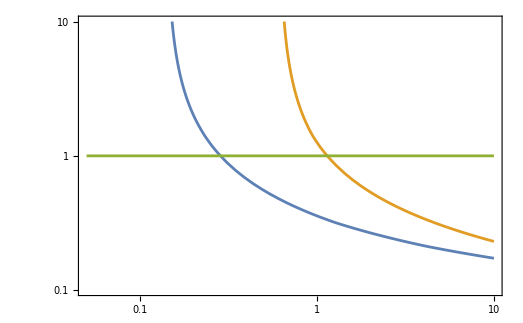

```mathematica
{(50TeV)/vEW*#⟦1⟧,#⟦2⟧}&/@QCDthrs;
LogLogPlot[{αsμ[μ,{Mpl,αQCDUV[Mpl],bQCDUV},QCDthrs],αsμ[μ,{Mpl,αQCDUV[Mpl],bQCDUV},%],1},{μ,0.05,10GeV},PlotRange->{{0.05,10GeV},{10^-1,10}},Frame->True]
```

## Dark QCD

A function to find v'_EW such that m'_q=Λ'_IR (i.e. the dark EW VEV above which the dark quark q' has a mass larger than the dark QCD scale and thus it must be integrated out for scales below its mass), i.e. the v'_EW at which a certain quark can be considered heavy. This is assuming Y'_i=Y_i.

```mathematica
Clear[vpHeavyQuark]

vpHeavyQuark[ithrs_,Λscale_:0]:=Block[{res,newthrs,ΛFn,LRV,LRVbench=2},

(*new thresholds, assuming dark EW VEV is v', and Subscript[y, q]'=Subscript[y, q]*)
newthrs[rv_]:={rv*#⟦1⟧,#⟦2⟧}&/@QCDthrs;

(*dark confinement scale: either computing it or given by hand*)
ΛFn[rv_?NumberQ,Λscale?NumberQ]:=If[Λscale==0,ΛIRpert[{newthrs[rv]⟦1,1⟧,αQCDUV[newthrs[rv]⟦1,1⟧],bQCDUV},newthrs[rv]],Λscale];

(*finding v' such that the i-th threshold matches the given confinement scale*)
res=10^(LRV/.FindRoot[ΛFn[10^LRV,Λscale]==newthrs[10^LRV]⟦ithrs,1⟧,{LRV,LRVbench}]);

res*vEW
]
```

### Tests

```mathematica
(*what value of v' makes Subscript[m, s]'=Subscript[Λ, IR]', with Subscript[Λ, IR]' obtained by perturbation theory?*)
vpHeavyQuark[4]

(*what value of v' makes Subscript[m, s]'=Subscript[Λ, IR]', with Subscript[Λ, IR]'=300 MeV [set by hand]?*)
vpHeavyQuark[4,300MeV]

(*what value of v' makes Subscript[m, s]'=Subscript[Λ, IR]', with Subscript[Λ, IR]'=1 GeV [set by hand]?*)
vpHeavyQuark[4,1GeV]
```

451.933

790.15

2633.83

```mathematica
(*what value of v' makes Subscript[m, s]'=Subscript[Λ, IR]'?*)
vpHeavyQuark[4]
%/vEW
{%*#⟦1⟧,#⟦2⟧}&/@QCDthrs;

(*Subscript[m, s]'*)
%⟦4,1⟧

(*Subscript[Λ, IR]'/Subscript[m, s]'*)
ΛIRpert[{%%⟦1,1⟧,αQCDUV[%%⟦1,1⟧],bQCDUV},%%]/%

(*what value of v' makes Subscript[m, d]'=Subscript[Λ, IR]'?*)
vpHeavyQuark[5]
%/vEW
{%*#⟦1⟧,#⟦2⟧}&/@QCDthrs;
(*Subscript[m, d]'*)

%⟦5,1⟧

(*Subscript[Λ, IR]'/Subscript[m, d]'*)
ΛIRpert[{%%⟦1,1⟧,αQCDUV[%%⟦1,1⟧],bQCDUV},%%]/%
```

451.933

1.83712

0.171587

1.

28296.6

115.027

0.537175

1.

{{21059.8,F},{509.756,F},{154.878,F},{11.3902,F},{0.569512,F},{0.263415,F}}

{21059.8,0.0684343,7}

0.547401

3.65189

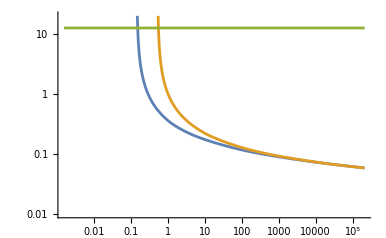

{0.0684343,0.0725541,0.0891461,0.0957367,0.107981,0.1179,0.211848,0.318434,12.5664}

```mathematica
newthrs={(30TeV)/vEW*#⟦1⟧,#⟦2⟧}&/@QCDthrs
newμαbUV={newthrs⟦1,1⟧,αQCDUV[newthrs⟦1,1⟧],bQCDUV}

Λ/.FindRoot[αsμ[Λ,newμαbUV,newthrs]==4π,{Λ,1}]
%/ΛIR
LogLogPlot[{αsμ[μ,newμαbUV,QCDthrs],αsμ[μ,newμαbUV,newthrs],4π},{μ,ΛIR/100,newthrs⟦1,1⟧*10},PlotRange->{10^-2,20}]

αsμ[#,newμαbUV,QCDthrs]&/@{newthrs⟦1,1⟧,10TeV,1TeV,500GeV,mt,mZ,mb,mc,ΛIR}

Clear[newthrs,newμαbUV]
```

## Λ'_QCD/Λ_QCD Ratio

Formulas for the ratio Λ'_QCD/Λ_QCD, assuming that:

1. All colored states above the top-quark are ℤ_2-symmetric: i.e. they have the same mass in the visible and dark sectors,
2. The calculations at 1-loop RG is enough

First formula: based on α_(s,UV):

```mathematica
Clear[ΛRFn1,ΛRFn2]
```

```mathematica
ΛRFn1[ΛQCD_,δα_,vP_,NHQ_,Yfac_,αsUV_]:=Block[{BIR=bQCDIR,BIRp=bs[3,0,6-NHQ],f1,f2,res},
(*assuming any colored states above the top-quark are Subscript[ℤ, 2]: i.e. they have the same mass in the visible and dark sectors*)

f1=Exp[(2π)/αsUV*δα];
f2=(((Times@@HeavyQuarks[NHQ])/(Times@@HeavyQuarks[3])*ΛQCD^(3-NHQ))(vP/vEW)^NHQ*Yfac^NHQ)^(2/3);
res=(f1*f2)^(1/BIRp);

Return[res]
]
```

Second formula: based on Λ_UV:

```mathematica
ΛRFn2[ΛUV_,ΛQCD_,δα_,vP_,NHQ_,Yfac_,NewStates_:{{1,0}}]:=Block[{BIR=bQCDIR,BIRp=bs[3,0,6-NHQ],αsIR=αQCDIR[ΛQCD],f1,f2,f3,f4,f5,res},
(*assuming any colored states above the top-quark are Subscript[ℤ, 2]: i.e. they have the same mass in the visible and dark sectors*)

f1=(ΛUV/ΛQCD)^(BIR*δα);
f2=(((Times@@HeavyQuarks[NHQ])/(Times@@HeavyQuarks[3])*ΛQCD^(3-NHQ))(vP/vEW)^NHQ*Yfac^NHQ)^(2/3);
f3=Exp[(2π)/αsIR*δα];
f4=Times@@((ΛUV/HeavyQuarks[3])^(-2/3*δα));
f5=((ΛUV/(#⟦1⟧))^(#⟦2⟧*δα)&)/@NewStates;
f5=Times@@f5;

res=(f1*f2*f3*f4*f5)^(1/BIRp);

Return[res]
]
```

#### (*Tests*)

```mathematica
(*αRun[Mpl,bs[3,0,6],αQCD[10TeV],10TeV]
(2π)/%
7*Log[Mpl]+(2π)/(4π)+Log[((Times@@HeavyQuarks[3])^(2/3))/ΛIR^9]*)
```

```mathematica
(*αRun[Mpl,bs[3,5,6],αQCDUV[10TeV],10TeV]
ΛRFn1[ΛIR,0.05,1TeV,3,2,%]
ΛRFn2[Mpl,ΛIR,0.05,1TeV,3,2,{{10TeV,-1/6},{10TeV,-1/6},{10TeV,-1/6},{10TeV,-1/6},{10TeV,-1/6}}]*)
```

```mathematica
(*αRun[Mpl,bs[3,5,6],αQCDUV[10TeV],10TeV]
ΛRFn1[ΛIR,0.05,1TeV,4,2,%]
ΛRFn2[Mpl,ΛIR,0.05,1TeV,4,2,{{10TeV,-1/6},{10TeV,-1/6},{10TeV,-1/6},{10TeV,-1/6},{10TeV,-1/6}}]*)
```

```mathematica
(*αRun[Mpl,bs[3,5,6],αQCDUV[10TeV],10TeV]
ΛRFn1[300MeV,0.05,1TeV,3,2,%]
ΛRFn2[Mpl,300MeV,0.05,1TeV,3,2,{{10TeV,-1/6},{10TeV,-1/6},{10TeV,-1/6},{10TeV,-1/6},{10TeV,-1/6}}]*)
```

```mathematica
(*αRun[Mpl,bs[3,1,6],αQCDUV[10TeV],10TeV]
ΛRFn1[ΛIR,0.02,1TeV,3,2,%]
ΛRFn2[Mpl,ΛIR,0.02,1TeV,3,2,{{10TeV,-1/6}}]*)
```

## Rates & Bounds

## Preamble

```mathematica
Clear[xsec,dec,kin,HProd,HpProd,HpRule1,HpRule2,HpRule10,HpRuleFn,ρRad,Hub,gsRule]
```

```mathematica
xsec=(((4π)/(64 π^2 s)*pf/pi M^2 v)/.{pi->m v,pf->m})
dec=((M^2/(32 π^2 m^2)*pf*4π)/.pf->m/2)
kin=√(1-(4 mfin^2)/m^2);
```

M^2/(16 π s)

M^2/(16 m π)

```mathematica
HProd=(βS*vew*y)/mhiggs^2;
HpProd=(βSp*vp*yp)/mhp^2;

HpRule1={βSp->100GeV,vp->1TeV,mhp->(1TeV)/vEW*mh,yp->yq[mb]};
HpRule2={βSp->100GeV,vp->2TeV,mhp->(2TeV)/vEW*mh,yp->yq[mb]};
HpRule10={βSp->100GeV,vp->10TeV,mhp->(10TeV)/vEW*mh,yp->yq[mb]};
HpRuleFn[vprime_]:={βSp->100 GeV,vp->vprime,mhp->mh*vprime/vEW,yp->yq[mb]}
```

```mathematica
ρRad[T_]:=(π^2 gs)/30 T^4
Hub[T_]:=√(ρRad[T]/(3 mpl^2))

gsRule={gχ->2,gR->1,gsTf->200,gssTf->200,gs->200,gss->200,gsvs->100,gssvs->100,gsds->100,gssds->100,gssf->100,gssτ->12};
```

## Generic freeze-out yield

Important prefactors

```mathematica
aPref=0.145*gχ/gss;
λPref=1.32*gss/(√gs);
```

Target Yields

```mathematica
Yχp/.Solve[ϵCP*mdb*Yχp*(s0tot/rs)==Ωdm*ρcrit,Yχp]⟦1⟧(*DM target Yield*)
%/.{rs->10,mdb->(Ωdm/Ωb)*mn,ϵCP->0.01}(*benchmark*)

Yχ/.Solve[ϵCP*mn*Yχ*(s0tot/rs)==Ωb*ρcrit,Yχ]⟦1⟧(*Baryon target Yield*)
%/.{rs->10,mb->mn,ϵCP->0.01}(*benchmark*)

aYRule={Yχ->%,a->aPref}(*a prefactor*);
```

(4.31476×10^-10 rs)/(mdb ϵCP)

8.6281×10^-8

(8.6281×10^-11 rs)/ϵCP

8.6281×10^-8

```mathematica
lam=λPref*mPl*mχ*σ0;
xfo=Log[aPref*lam]-1/2 Log[Log[aPref*lam]];
Yχ=xfo/lam

(aPref*lam)/.gsRule~Join~{mχ->3TeV,σ0->10^-15 GeV^-2,mPl->mpl}
xfo/.gsRule~Join~{mχ->3TeV,σ0->10^-15 GeV^-2,mPl->mpl}
Yχ/.gsRule~Join~{mχ->3TeV,σ0->10^-15 GeV^-2,mPl->mpl}

(*Clear[lam,xfo,Yχ]*)
```

(0.757576 √gs (Log[(0.1914 gχ mPl mχ σ0)/(√gs)]-1/2 Log[Log[(0.1914 gχ mPl mχ σ0)/(√gs)]]))/(gss mPl mχ σ0)

197762.

10.9443

8.02444×10^-8

```mathematica
(*Log[a/Yχ]/.aYRule(*log(a/Subscript[Y, χ])*)
%/.gsRule(*benchmark*)
%%/Yχ/.aYRule(*λ≡(ln(a/Subscript[Y, χ]))/Subscript[Y, χ]*)
%/.gsRule(*benchmark*)
Log[a*%%]/.aYRule(*Subscript[x, fo]≡ln(aλ)*)
%/.gsRule(*like*)

σ0/.Solve[λPref*mpl*mχ*σ0==%%%,σ0]⟦1⟧(*target cross section*)
%/.(gsRule~Join~{mχ->3TeV})(*benchmark*)*)
```

## χ annihilations

### Heavy S

```mathematica
σχhHs=xsec/.{s->(2mχ)^2,M->(mχ*α*1/mS^2*βS)}(*χχ->hh*)
(*σχhHs/.({α->1,mχ->3.TeV,βS->200GeV,mS->20.TeV}~Join~HpRule1)(*bench. Subscript[σ, χh] [GeV^-2]*)*)
σχhHs/.({α->0.5,mχ->3.TeV,βS->100GeV,mS->10.TeV}~Join~HpRule1)(*bench. Subscript[σ, χh] [GeV^-2]*)
```

(α^2 βS^2)/(64 mS^4 π)

1.2434×10^-15

```mathematica
σχfpHs=xsec/.{s->(2mχ)^2,M->(mχ*α*1/mS^2*HpProd*mχ)}(*χχ->f' f'*)
(σχfpHs/.({α->0.5,mχ->3.TeV,βS->100GeV,mS->10TeV}~Join~HpRule1))*(1/11)(*bench. Subscript[σ, χf'] [GeV^-2]*)
```

(mχ^2 vp^2 yp^2 α^2 βSp^2)/(64 mhp^4 mS^4 π)

8.74182×10^-18

### ***TODO: Light S

```mathematica
(*σχs=xsec/.{s->(2mχ)^2,M->(mχ*1/mχ α^2)}(*χχ->SS*)
σχs/.{α->1.,mχ->5TeV}(*bench. Subscript[σ, χS] [GeV^-2]*)*)
```

```mathematica
(*σχhLs=xsec/.{s->(2mχ)^2,M->(mχ*α*1/mχ^2*βS)}(*χχ->hh*)
σχhLs/.{α->1.,mχ->2TeV,βS->100GeV}(*bench. Subscript[σ, χh] [GeV^-2]*)*)
```

```mathematica
(*σχfpLs=xsec/.{s->(2mχ)^2,M->(mχ*α*1/mχ^2*HpProd*mχ)}(*χχ->f' f'*)
(σχfpLs/.{α->1,mχ->5.TeV,βS->100GeV,βSp->100GeV,vp->30TeV,mhp->(30TeV)/vEW*mh,yp->yq[mb]})*(3/30)(*bench. Subscript[σ, χf'] [GeV^-2]*)*)
```

## χ decays & (dark) baryogenesis

```mathematica
Clear[ΓχLϕ,εBBNLϕ,εfoLϕ,FSLϕ,FVLϕ,ϵCPLϕ,ΓχHϕ,εBBNHϕ,εfoHϕ,FSHϕ,FVHϕ,ϵCPHϕ]
```

### Light ϕ

```mathematica
ΓχLϕ=2*(dec/.{m->mχ,M->mχ*ε})(*χ decay rate*)
εBBNLϕ=(ε/.Solve[ΓχLϕ==1 sec^-1,ε]⟦2⟧//FullSimplify(*before BBN*))
εfoLϕ=(ε/.Solve[ΓχLϕ==Hub[mχ/11],ε]⟦2⟧//FullSimplify(*after freeze-out*))

{εBBNLϕ,εfoLϕ}
%/.{mχ->3.TeV}~Join~gsRule
GeometricMean[%]
ΓχLϕ/.{mχ->3TeV,ε->%}
```

(mχ ε^2)/(8 π)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Part::partw: Part 2 of {{ε→(4.06727×10^-12)/(√mχ)}} does not exist.

ReplaceAll::reps: {{{ε→(4.06727×10^-12)/(√mχ)}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ε/.{{ε→(4.06727×10^-12)/(√mχ)}}⟦2⟧

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Part::partw: Part 2 of {{ε→Root[-64. gs Power[«2»]+8.02308×10^40 Power[«2»]&,2]}} does not exist.

ReplaceAll::reps: {{{ε→Root[Plus[«2»]&,2]}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ε/.{{ε→Root[-64. gs mχ^2+8.02308×10^40 #1^4&,2]}}⟦2⟧

{ε/.{{ε→(4.06727×10^-12)/(√mχ)}}⟦2⟧,ε/.{{ε→Root[-64. gs mχ^2+8.02308×10^40 #1^4&,2]}}⟦2⟧}

Part::partw: Part 2 of {{ε→7.42578×10^-14}} does not exist.

ReplaceAll::reps: {{{ε→7.42578×10^-14}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {{ε→3.46161×10^-8}} does not exist.

ReplaceAll::reps: {{{ε→3.46161×10^-8}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{ε/.{{ε→7.42578×10^-14}}⟦2⟧,ε/.{{ε→3.46161×10^-8}}⟦2⟧}

√((ε/.{{ε→7.42578×10^-14}}⟦2⟧) (ε/.{{ε→3.46161×10^-8}}⟦2⟧))

1/π 375 (ε/.{{ε→7.42578×10^-14}}⟦2⟧) (ε/.{{ε→3.46161×10^-8}}⟦2⟧)

The net baryon asymmetry produced in the decays is

ϵ_CP=1/(8π)*(Im{(Σ_i ε_i y_i^*)^2})/(Σ_i|ε_i|^2)[3ℱ_S(m_ψ^2/m_χ^2)+ℱ_V(m_ψ^2/m_χ^2)]

which depends on the functions

```mathematica
FSLϕ[x_]:=1/2(√x)/(1-x)(*from 9605319 & 1312.1334, but correcting for lack of SU(2) numbers. Note that Burdman had other functions: those for the SUSY case of 9605319*)
FVLϕ[x_]:=√x(1-(1+x)Log[1+1/x])(*from 9605319. Note that Burdman had other functions: those for the SUSY case of 9605319*)
```

which in the hierarchical limit give

```mathematica
Normal@Series[3FSLϕ[μ^2]+FVLϕ[μ^2],{μ,∞,1}]
```

-2/μ

In this same limit, and for ε_i<<1, we can then approximate ϵ_CP as

```mathematica
ϵCPLϕ=2/(8π)y^2 mχ/mψ;
ϵCPLϕ/.{mχ->3TeV,y->1,mψ->10.TeV}
```

0.0238732

```mathematica
Normal@Series[√x(1-(1+x)Log[1+1/x]),{x,∞,1}]
```

-1/(2 √x)

### ***TODO: Heavy ϕ

```mathematica
(*ΓχHϕ=2*(dec/.{m->mχ,M->mχ^3/mϕ^2*ε*y})(*χ decay rate*)
εBBNHϕ=(ε/.Solve[ΓχHϕ==1 sec^-1,ε]⟦2⟧//FullSimplify(*before BBN*))
εfoHϕ=(ε/.Solve[ΓχHϕ==Hub[mχ/11],ε]⟦2⟧//FullSimplify(*after freeze-out*))

{εBBNHϕ,εfoHϕ}
%/.{mχ->3.TeV,mϕ->10.TeV,y->1}~Join~gsRule
GeometricMean[%]
ΓχHϕ/.{mχ->3TeV,ε->%,mϕ->10TeV,y->1}*)
```

The net baryon asymmetry produced in the decays is

ϵ_CP=1/(8π)*(Im{(Σ_i ε_i y_i^*)^2})/(Σ_i|ε_i|^2)[3ℱ_S(m_ψ^2/m_χ^2)+ℱ_V(m_ψ^2/m_χ^2)]

which depends on the functions

```mathematica
(*FSHϕ[x_]:=(2 √x)/(x-1)
FVHϕ[x_]:=√x Log[1+1/x]*)
```

which in the hierarchical limit give

```mathematica
(*Normal@Series[3FS[μ^2]+FV[μ^2],{μ,∞,1}]*)
```

In this same limit, and for ε_i<<1, we can then approximate ϵ_CP as

```mathematica
(*ϵCPHϕ=7/(8π)y^2 mχ/mψ;
ϵCPHϕ/.{mχ->3TeV,y->0.5,mψ->10.TeV}*)
```

## Asymmetric Reheating

### Preamble

m_h' for v'=30 TeV:

```mathematica
mh*(30TeV)/vEW/TeV(*bench. Subscript[m, h'] [TeV]*)
```

15.2744

m_h' for v'=1 TeV:

```mathematica
mh*(1TeV)/vEW/TeV(*bench. Subscript[m, h'] [TeV]*)
```

0.509146

Hubble at m_r:

```mathematica
Hub[mR]//Simplify
%/.{mR->500GeV}~Join~gsRule(*bench. H [GeV]*)
```

1.35977×10^-19 √gs mR^2

4.80751×10^-13

Hubble at T=1MeV

```mathematica
(*1/2**)((Hub[1MeV]/.{gs->2+7/8*(2(*γ*)*3(*ν*)+2*2*3(*e*))})*sec)^-1(* 1/Hubble [sec] at T=1 MeV*)
```

1.14895

### Reheaton domination

Temperature T_(R-dom) at which R dominates the Universe

```mathematica
Clear[TRdom]

(mR*nr)/.{nr->1*ncoeff*T^3*gsTeq/gssTf}
T/.Solve[(ρRad[T]/.gs->gsTeq)==%,T]⟦-1⟧
TRdom=%;(*Subscript[T, Rdom]*)

%/.{mR->0.7TeV}~Join~(gsRule)(*bench. Subscript[T, Rdom] [GeV]*)
```

(gsTeq mR T^3 Zeta[3])/(gssTf π^2)

(30 mR Zeta[3])/(gssTf π^4)

1.29573

### Reheaton decay

```mathematica
Clear[ΓRh,benchΓRh,ΓRf,benchΓRfp,ΓRvs,ΓRds,ΓRtot,RBRvs,RBRds]
```

#### Reheaton Decay Rates & Branching Ratios

R decay rates

```mathematica
Clear[ΓRh,benchΓRh,ΓRf,benchΓRfp]

ΓRh=(dec*kin*ThetaFn[m-2mfin])/.{m->mR,M->βR,mfin->mH}(*R->h^(′)h^(′)*)
benchΓRh=(ΓRh/.{βR->10.eV,mR->0.7TeV,mH->mh})(*bench. Subscript[Γ, Rh] [GeV]*)

ΓRf=3(*Subscript[N, c]^(′)*)*(((dec*kin^3*ThetaFn[m-2*mfin])/.{m->mR,M->(v*yuk*βR*mR)/(√((mR^2-mH^2)^2+mH^2 ΓH^2)),mfin->(v*yuk)/(√2)}))(*R->f^(′)f^(′)*)
benchΓRfp=(ΓRf/.({mR->0.7TeV,βR->10.eV,mH->(1TeV)/vEW*mh,yuk->yq[mb],v->1TeV,ΓH->Γh*(1TeV)/vEW}))
```

1/(16 mR π)√(1-(4 mH^2)/mR^2) βR^2 If[-2 mH+mR==0,0,HeavisideTheta[mR-2 mH]]

2.65384×10^-21

(3 mR v^2 yuk^2 (1-(2 v^2 yuk^2)/mR^2)^(3/2) βR^2 If[mR-√2 v yuk==0,0,HeavisideTheta[mR-(2 (v yuk))/(√2)]])/(16 π ((-mH^2+mR^2)^2+mH^2 ΓH^2))

4.51404×10^-23

```mathematica
Clear[ΓRvs,ΓRds,ΓRtot,RBRvs,RBRds]

ΓRvs[br_,mr_]:=Re[(ΓRh+(ΓRf/.yuk->yq[mb])+(ΓRf/.yuk->yq[mt]))/.{mH->mh,v->vEW,ΓH->Γh,mR->mr,βR->br}];
ΓRds[βRp_,mr_,vP_,yFac_]:=Re[(ΓRh+ΓRf)/.{mR->mr,βR->βRp,mH->mh*vP/vEW,v->vP,ΓH->Γh*vP/vEW,yuk->yq[mb]*yFac}];
ΓRtot[βR_,βRp_,mR_,vP_,yFac_]:=ΓRvs[βR,mR]+ΓRds[βRp,mR,vP,yFac];
RBRvs[βR_,βRp_,mR_,vP_,yFac_]:=ΓRvs[βR,mR]/ΓRtot[βR,βRp,mR,vP,yFac];
RBRds[βR_,βRp_,mR_,vP_,yFac_]:=ΓRds[βRp,mR,vP,yFac]/ΓRtot[βR,βRp,mR,vP,yFac];
```

#### Simplified expressions

Simplifying assumptions:
1. Massless final states (m_h,m_f<<m_R)
2. VS dominant channel: R→hh
3. DS dominant channel: R→f' OverBar[f']

```mathematica
Clear[RHSimple,ΓRhSimple,ΓRfpSimple]

RHSimple[fn_]:=Assuming[(mR>0)&&(mR>√2 v*yuk),(fn)//Simplify]

ΓRhSimple=RHSimple[Taylor[ΓRh,mH]]
ΓRfpSimple=(RHSimple[Taylor[Taylor[ΓRf,ΓH],yuk,0,2]]/.{βR->βRp,v->vp,yuk->yp,mH->mhp})
Taylor[(%/.mR->r*mhp)/.{r->1+ϵ},ϵ,0,-2]
```

βR^2/(16 mR π)

(3 mR vp^2 yp^2 βRp^2)/(16 (mhp^2-mR^2)^2 π)

(3 vp^2 yp^2 βRp^2)/(64 mhp^3 π ϵ^2)

```mathematica
benchΓRh
ΓRhSimple/.{βR->10.eV,mR->0.7TeV}

benchΓRfp
ΓRfpSimple/.{βRp->10.eV,mR->0.7TeV,vp->1TeV,yp->yq[mb],mhp->mh*(1TeV)/vEW}
```

2.65384×10^-21

2.84205×10^-21

4.51404×10^-23

4.53005×10^-23

#### Plots

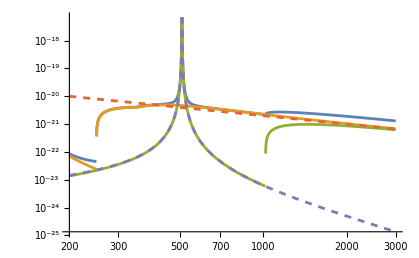

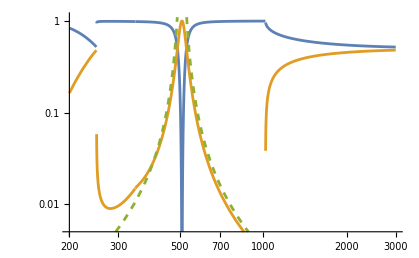

```mathematica
brT=10eV;
vpT=1TeV;

LogLogPlot[{ΓRtot[brT,brT,mR,vpT,1],ΓRvs[brT,mR],ΓRds[brT,mR,vpT,1],ΓRhSimple/.{βR->brT},ΓRfpSimple/.{βRp->brT,vp->vpT,mhp->mh*vpT/vEW,yp->yq[mb]}},{mR,200GeV,3*vpT},PlotStyle->{Automatic,Automatic,Automatic,Dashed,Dashed}]

LogLogPlot[{RBRvs[brT,brT,mR,vpT,1],RBRds[brT,brT,mR,vpT,1],(ΓRfpSimple/ΓRhSimple/.{βR->brT,βRp->brT,vp->vpT,mhp->mh*vpT/vEW,yp->yq[mb]})},{mR,200GeV,3*vpT},PlotStyle->{Automatic,Automatic,Dashed},PlotRange->{0.005,1.1}]

Clear[brT,vpT]
```

#### Simplified bounds on β_R

```mathematica
Clear[βRRdom]

βRRdom=((βR/.Solve[ΓRhSimple==Hub[TRdom],βR]⟦2⟧)//FullSimplify)(*demanding Subscript[β, R] such that Subscript[T, Rdec]<Subscript[T, R-dom]*)
βRBBN=((βR/.Solve[ΓRhSimple==1 sec^-1,βR]⟦2⟧)//FullSimplify)(*demanding larger before BBN*)
({βRBBN/eV,βRRdom/eV}/.{mR->0.7TeV,gssTf->200,gs->200})(*bench. Subscript[β, R] [eV, eV]*)
(%⟦2⟧*eV)/(%⟦1⟧*eV)(*"room" in parameter space: ratio between upper and lower bound*)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Part::partw: Part 2 of {{βR→Root[-256. gs Power[«2»]+2.91731×10^38 Power[«2»] Power[«2»]&,2]}} does not exist.

ReplaceAll::reps: {{{βR→Root[Plus[«2»]&,2]}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

βR/.{{βR→Root[-256. gs mR^6+2.91731×10^38 gssTf^4 #1^4&,2]}}⟦2⟧

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Part::partw: Part 2 of {{βR→5.75198×10^-12 √mR}} does not exist.

ReplaceAll::reps: {{{βR→5.75198×10^-12 √mR}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

βR/.{{βR→5.75198×10^-12 √mR}}⟦2⟧

Part::partw: Part 2 of {{βR→1.52183×10^-10}} does not exist.

ReplaceAll::reps: {{{βR→1.52183×10^-10}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {{βR→3.37046×10^-7}} does not exist.

ReplaceAll::reps: {{{βR→3.37046×10^-7}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{1000000000 (βR/.{{βR→1.52183×10^-10}}⟦2⟧),1000000000 (βR/.{{βR→3.37046×10^-7}}⟦2⟧)}

(βR/.{{βR→3.37046×10^-7}}⟦2⟧)/(βR/.{{βR→1.52183×10^-10}}⟦2⟧)

Decays to VS should dominate:

In terms of m_R:

```mathematica
Clear[mRVSdom]
ΓRfpSimple/.{βRp^2->bp2,mR->√m2,mhp^2->mh2,yp^2->y2,vp^2->v2}
ΓRhSimple/.{βR^2->b2,mR->√m2,mhp^2->mh2,yp^2->y2,vp^2->v2}
m2/.#&/@Solve[%%==%,m2];
Taylor[#,y2]&/@%;
(%/.{b2->βR^2,bp2->βRp^2,m2->mR^2,mh2->mhp^2,y2->yp^2,v2->vp^2})//FullSimplify
mRVSdom=(Taylor[√#,yp]&/@%)
(mRVSdom/.{βR->10eV,βRp->10eV,yp->yq[mb],vp->1TeV,mhp->mh(1TeV)/vEW})
%-mh(1TeV)/vEW
```

(3 bp2 √m2 v2 y2)/(16 (-m2+mh2)^2 π)

b2/(16 √m2 π)

{mhp^2-(√3 mhp vp yp βRp)/βR+(3 vp^2 yp^2 βRp^2)/(2 βR^2),mhp^2+(√3 mhp vp yp βRp)/βR+(3 vp^2 yp^2 βRp^2)/(2 βR^2)}

{mhp-(√3 vp yp βRp)/(2 βR),mhp+(√3 vp yp βRp)/(2 βR)}

{488.336,529.957}

{-20.8107,20.8107}

In terms of β'_R:

```mathematica
Clear[βRpVSdom]

βRpVSdom=(βRp/.Solve[ΓRfpSimple==ΓRhSimple,βRp]⟦2⟧)(*demanding R->f' f' as important as R->hh*)
(%/.(HpRule1~Join~{mR->0.7TeV(*,βR->10.eV*)}))(*/eV*)(*bench. Subscript[β, r]'*)
(%/.{βR->10.eV})/eV(*bench. Subscript[β, r]' [eV]*)
```

Part::partw: Part 2 of {{βRp→(√(Power[«2»] Power[«2»]-«1»+Power[«2»] Power[«1»]))/(√3 mR vp yp)}} does not exist.

ReplaceAll::reps: {{{βRp→(√Plus[«3»])/(√3 mR vp yp)}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

βRp/.{{βRp→(√(mhp^4 βR^2-2 mhp^2 mR^2 βR^2+mR^4 βR^2))/(√3 mR vp yp)}}⟦2⟧

Part::partw: Part 2 of {{βRp→7.92072 √(βR^2)}} does not exist.

ReplaceAll::reps: {{{βRp→7.92072 √Power[«2»]}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

βRp/.{{βRp→7.92072 √(βR^2)}}⟦2⟧

Part::partw: Part 2 of {{βRp→7.92072×10^-8}} does not exist.

ReplaceAll::reps: {{{βRp→7.92072×10^-8}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

1000000000 (βRp/.{{βRp→7.92072×10^-8}}⟦2⟧)

#### Reheaton & Temperature when H=Γ_R (denoted by τ)

The reheaton energy density at the time t=τ when H=Γ_R (not t=Γ_R^-1) in the instantaneous decay approximation (IDA), and the thermal bath temperature at that time. Note that we are currently not distinguishing between T_τ and T'_τ, which are different because g_(*s)≠g'_(*s) due to the latter’s heavier mass thresholds: the VS plays catch-up to the DS since g'_(*s) drops before g_(*s) in each threshold. We however assume that it catches up rather quickly. This dynamics stops after RH (the instant after τ) due to asymmetric reheating.

For the same reason we will also simply assume that, from VS-DS recoupling down to τ, entropy is conserved in both sectors, and that catch-up happens quickly, so

g_(*s)^tot=g_(*s)(1+S'/S)=2 g_(*s),
and
g_*^tot=g_*(1+((g'_*)/(g_*))((g_(*s))/(g'_(*s)))^(4/3)(S'/S)^(4/3))=g_*(1+((g'_*)/(g_*))((g_(*s))/(g'_(*s)))^(4/3))≈2 g_*.

```mathematica
Clear[ρRτ,Tτ]

ρRτ[βR_,βRp_,mR_,vP_,yFac_]:=(3*mpl^2*ΓRtot[βR,βRp,mR,vP,yFac]^2)
Tτ[βR_,βRp_,mR_,vP_,yFac_,gssf_:gSM]:=Block[{br=βR,brp=βRp,mr=mR,vprime=vP,yfac=yFac,gStarSFO=gssf,rhs,LT,res},
rhs=gssf/(ncoeff*1)*ρRτ[βR,βRp,mR,vP,yFac]/mR;
(*res=10^(LT/.FindRoot[gsFn[10^LT] 10^(3LT)==rhs,{LT,0}]);*)
res=10^(LTgT3[Log10[rhs]]);

res
]
```

### Reheating Radiation Density and Temperature

#### Energy Density

```mathematica
Clear[ρrhVS,ρrhDS]

ρrhVS[βR_,βRp_,mR_,vP_,yFac_,gssf_:gSM]:=Block[{br=βR,brp=βRp,mr=mR,vprime=vP,yfac=yFac,gStarSFO=gssf,rhoRτ,BR,Tempτ,res},

rhoRτ=ρRτ[br,brp,mr,vprime,yfac];
BR=RBRvs[br,brp,mr,vprime,yfac];
Tempτ=Tτ[br,brp,mr,vprime,yfac,gStarSFO];

res=rhoRτ(BR+ρcoeff/(ncoeff*1)^(4/3)*gsFn[Tempτ]*(gStarSFO/gsFn[Tempτ])^(4/3)(rhoRτ/mr^4)^(1/3));
res
]

ρrhDS[βR_,βRp_,mR_,vP_,yFac_,gssf_:gSM]:=Block[{br=βR,brp=βRp,mr=mR,vprime=vP,yfac=yFac,gStarSFO=gssf,rhoRτ,BR,Tempτ,res},

rhoRτ=ρRτ[br,brp,mr,vprime,yfac];
BR=RBRds[br,brp,mr,vprime,yfac];
Tempτ=Tτ[br,brp,mr,vprime,yfac,gStarSFO];

res=rhoRτ(BR+ρcoeff/(ncoeff*1)^(4/3)*gsFn[Tempτ]*(gStarSFO/gsFn[Tempτ])^(4/3)(rhoRτ/mr^4)^(1/3));
res
]
```

#### Temperature

The corresponding temperature, and a simple approximation for it

```mathematica
Clear[TrhVS,TrhDS,TrhSimple]

TrhVS[βR_,βRp_,mR_,vP_,yFac_,gssf_:gSM]:=Block[{br=βR,brp=βRp,mr=mR,vprime=vP,yfac=yFac,gStarSFO=gssf,rhs,LT,res},

rhs=1/ρcoeff ρrhVS[br,brp,mr,vprime,yfac,gStarSFO];

(*res=(10^LT/.FindRoot[gsFn[10^LT]*10^(4LT)==rhs,{LT,0}]);*)
res=(10^LTgT4[Log10[rhs]]);

res
]


TrhDS[βR_,βRp_,mR_,vP_,yFac_,gssf_:gSM]:=Block[{br=βR,brp=βRp,mr=mR,vprime=vP,yfac=yFac,gStarSFO=gssf,rhs,LT,res},

rhs=1/ρcoeff ρrhDS[br,brp,mr,vprime,yfac,gStarSFO];

(*res=(10^LT/.FindRoot[gsFn[10^LT]*10^(4LT)==rhs,{LT,0}]);*)
res=(10^LTgT4[Log10[rhs]]);

res
]


TrhSimple=((90*ΓRhSimple^2*mpl^2)/(gsrh*π^2))^(1/4)//FullSimplify
```

(3.82501×10^8 βR)/(gsrh^(1/4) √mR)

```mathematica
TrhVS[10eV,10eV,0.7TeV,1TeV,1,100]
gsFn[%]
TrhSimple/.{βR->10eV,mR->0.7TeV,gsrh->16}
```

0.0789514

16.3176

0.0722859

Some plots

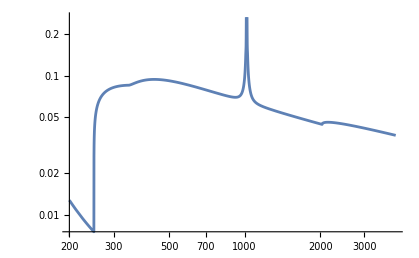

```mathematica
brT=10eV;
vpT=2TeV;
gsT=16;


TrhTest[mR_]:=TrhVS[brT,brT,mR,vpT,1]

LogLogPlot[{TrhTest[mR],(TrhSimple/.{βR->brT,gsvs->gsT})},{mR,200GeV,2*vpT}]

Clear[brT,vpT,gsT,TrhTest]
```

#### g_(*,rh)^tot

```mathematica
Clear[gsrhTot]

gsrhTot[βR_,βRp_,mR_,vP_,yFac_,gssf_:gSM]:=Block[{br=βR,brp=βRp,mr=mR,vprime=vP,yfac=yFac,gStarSFO=gssf,TempVS,gsVS,TempDS,gsDS,res},

TempVS=TrhVS[br,brp,mr,vprime,yfac,gStarSFO];
gsVS=gsFn[TempVS];

TempDS=TrhDS[br,brp,mr,vprime,yfac,gStarSFO];
gsDS=gsFn[TempDS];

res=gsVS+gsDS*(TempDS/TempVS)^3;

res
]
```

### Dark Radiation

#### D.O.F. Ratios

```mathematica
Clear[Gratio,GValue]

Gratio[g0VS_?ListQ,g0DS_?ListQ,grhVS_?ListQ,grhDS_?ListQ]:=(g0DS⟦1⟧/g0VS⟦1⟧*grhVS⟦1⟧/grhDS⟦1⟧)(g0VS⟦2⟧/g0DS⟦2⟧*grhDS⟦2⟧/grhVS⟦2⟧)^(4/3)(*{g_(*e),g_(*s)}*)

GValue[βR_,βRp_,mR_,vP_,yFac_,gssf_:gSM]:=Block[{br=βR,brp=βRp,mr=mR,vprime=vP,yfac=yFac,gStarSFO=gssf,TempVS,gsVS,TempDS,gsDS,res},

TempVS=TrhVS[br,brp,mr,vprime,yfac,gStarSFO];
gsVS=gsFn[TempVS];

TempDS=TrhDS[br,brp,mr,vprime,yfac,gStarSFO];
gsDS=gsFn[TempDS];

res=Gratio[{ge0,gs0},{ge0,gs0},{gsVS,gsVS},{gsDS,gsDS}];

res
]
```

#### ΔN_eff

```mathematica
Clear[ΔNeff,term1,term2,ΔNdsSimple]

ΔNeff[βR_?NumberQ,βRp_?NumberQ,mR_?NumberQ,vP_?NumberQ,yFac_?NumberQ,gssf_:gSM]:=ΔNeff[βR,βRp,mR,vP,yFac,gssf]=(ge0/ge1ν)*GValue[βR,βRp,mR,vP,yFac,gssf]*(ρrhDS[βR,βRp,mR,vP,yFac,gssf]/ρrhVS[βR,βRp,mR,vP,yFac,gssf])

term1=ΓRfpSimple/ΓRhSimple(*if 2 Subscript[m, h]'>Subscript[m, R]*)
term2=(ρcoeff*(gssf^4/gssτ)^(1/3)*((3 mpl^2 ΓRhSimple^2)/(ncoeff*mR)^4)^(1/3))//FullSimplify
ΔNdsSimple=(ge0/ge1ν)(term1+term2)
```

(3 mR^2 vp^2 yp^2 βRp^2)/((mhp^2-mR^2)^2 βR^2)

1.04451×10^12 ((gssf^4 βR^4)/(gssτ mR^6))^(1/3)

7.44142 (1.04451×10^12 ((gssf^4 βR^4)/(gssτ mR^6))^(1/3)+(3 mR^2 vp^2 yp^2 βRp^2)/((mhp^2-mR^2)^2 βR^2))

```mathematica
term1/.(gsRule~Join~HpRule1~Join~{βR->10.eV,βRp->10.eV,mR->0.7TeV})
(ge0/ge1ν)*%
term2/.(gsRule~Join~HpRule1~Join~{βR->10.eV,βRp->10.eV,mR->0.7TeV})
(ge0/ge1ν)*%

ΔNdsSimple/.(gsRule~Join~HpRule1~Join~{βR->10.eV,βRp->10.eV,mR->0.7TeV})
ΔNeff[βR,βR,mR,vp,1]/.(HpRule1~Join~{βR->10.eV,βRp->10.eV,mR->0.7TeV})
```

0.0159394

0.118611

0.00931089

0.0692862

0.187898

0.169509

Some more plots

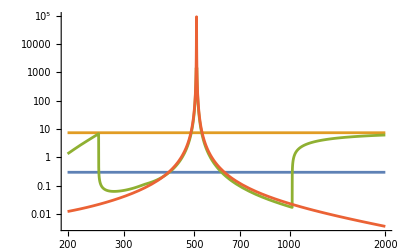

```mathematica
brT=0.1eV;
vpT=1TeV;
ypT=yq[mb];

LogLogPlot[{0.3,(ge0/ge1ν),ΔNeff[brT,brT,mR,vpT,1],(ΔNdsSimple/.{βR->brT,βRp->brT,yp->ypT,vp->vpT,mhp->mh*vpT/vEW,gssτ->16,gssf->100})},{mR,200GeV,2*vpT}]

Clear[brT,vpT,ypT]
```

#### DR temperature today: T'_0(ΔN_eff)

T' for a given ΔN_eff, for DR consisting of a dark photon & 3 neutrinos:

```mathematica
Clear[Tprime0]

Tprime0[ΔN_]:=(Tp0/.Solve[ΔN*ge1ν*ρcoeff*Tγ0^4==(2+3*ge1ν)*ρcoeff*Tp0^4,Tp0,Reals]⟦2⟧)
```

```mathematica
Tprime0[0.284]/Tγ0
Tprime0[0.463]/Tγ0
```

0.442563

0.500081

Some examples:

```mathematica
(*Subscript[ΔN, eff]=0.3*)
(2+3*2*7/8*(4/11))*scoeff*Tprime0[0.3]^3
%/(s0tot+%)
```

2.00645×10^-39

0.0822403

```mathematica
(*example parameters*)
ΔNeff[10eV,10eV,0.7TeV,1TeV,1]
(2+3*2*7/8*(4/11))*scoeff*Tprime0[%]^3
%/(s0tot+%)
```

0.169509

1.30762×10^-39

0.0551771

### Entropy dump

```mathematica
Clear[SDump,SDumpSimple]

SDump[βR_,βRp_,mR_,vP_,yFac_,gssf_:gSM]:=Block[{br=βR,brp=βRp,mr=mR,vprime=vP,yfac=yFac,gStarSFO=gssf,rhoRτ,gssTot,res},

rhoRτ=ρRτ[br,brp,mr,vprime,yfac];
gssTot=gsrhTot[br,brp,mr,vprime,yfac,gStarSFO];

res=(1+4/3*1.09*scoeff^(1/3)*((mr^4(ncoeff/(2*gStarSFO*scoeff))^4)/rhoRτ)^(1/3)*gssTot^(1/3))^(3/4)(*entropy ratio, Kolb's Eq. 5.71*);

res
]

SDumpSimple=(1.83(ncoeff/(gssTf*scoeff))*gssrh^(1/4)*mR/(√(ΓRhSimple*Mpl))//FullSimplify)(*entropy ratio, Kolb's Eq. 5.73*)
```

(1.03098×10^-9 gssrh^(1/4) mR^(3/2))/(gssTf βR)

```mathematica
SDump[βR,βR,mR,vP,yFac,gSM]/.{mR->0.7TeV,βR->10.eV,vP->1TeV,yFac->1}(*benchmark*)
SDumpSimple/.{mR->0.7TeV,βR->10.eV}~Join~{gssrh->17,gssTf->200}(*benchmark*)
```

16.9179

19.3857

More plots

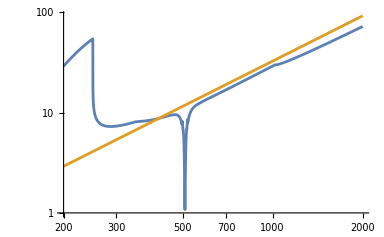

```mathematica
brT=10eV;
vpT=1TeV;

LogLogPlot[{SDump[brT,brT,mR,vpT,1],SDumpSimple/.{βR->brT,gssrh->16,gssTf->200}},{mR,200GeV,2*vpT}]

Clear[brT,vpT]
```

### DS-VS thermal equilibrium

#### Generic heavy mediator

Cross section and corresponding thermal decoupling for a generic heavy mediator

```mathematica
Clear[MHovergBound]

xsec/.{s->(2T)^2,M->T^2/MHg^2}
(MHg/.Solve[((%*ncoeff*T^3)/.T->TRdom)==(Hub[TRdom]/.gs->gsTReq),MHg]⟦-1⟧)//FullSimplify
MHovergBound=(%/.{gssTf->200,gsTReq->2gsFn[1GeV],mR->700GeV})
```

T^2/(64 MHg^4 π)

(3877.42 (mR/gssTf)^(3/4))/gsTReq^(1/8)

5300.63

The corresponding bound on a Higgs-dark Higgs coupling λ_HH':

```mathematica
Clear[λHHpBound]
λHHpBound=(λHHp/.Solve[((λHHp*yp*yq[mc]*vEW*vp)/(mh^2(mh*vp/vEW)^2))==MHovergBound^-2,λHHp]⟦1⟧)
λHHpBound/.{gssTf->200,gsTReq->2gsFn[1GeV],mR->700GeV,yp->yq[mc],vp->1TeV}
```

(0.0000805873 vp)/yp

11.0378

The effective λ_HH' induced by the reheaton

```mathematica
(βR*βRp)/mR^2/.{βR->10eV,βRp->10eV,mR->700.GeV}
```

2.04082×10^-22

#### Specific interactions

Through generic Higgs-dark Higgs λ_HH' coupling: ff̄⟷f' OverBar[f']

```mathematica
σffp=((xsec/.{s->(2T)^2,M->T*HProd*1/mS^2*HpProd*T})(**3/3^2*))/.{βS->λhhp*mS^2/βSp}
σffp/.({vew->vEW,mhiggs->mh,y->yq[mb],λhhp->10^-4,vp->1TeV,mhp->(1TeV)/vEW mh,yp->yq[mb]})
%/.T->100GeV
(λhhp/.Solve[(σffp/.{T->TRdom,vew->vEW,mhiggs->mh,y->yq[mc]})*(ncoeff*TRdom^3)==Hub[TRdom],λhhp]⟦-1⟧)//FullSimplify
%/.{mR->0.7TeV,vp->1TeV,mhp->(1TeV)/vEW mh,yp->yq[mb]}~Join~gsRule
%%/.{mR->0.7TeV,vp->1TeV,mhp->(1TeV)/vEW mh,yp->yq[mqs]}~Join~{gssTf->200,gs->200}
(1TeV)/vEW*mqs
```

(T^2 vew^2 vp^2 y^2 yp^2 λhhp^2)/(64 mhiggs^4 mhp^4 π)

6.06853×10^-26 T^2

6.06853×10^-22

(0.000580967 gs^(1/4) mhp^2 (gssTf/mR)^(3/2))/(vp yp)

3.59945

{6965.6,3221.78,161.089,11.847,3.59945,0.0871254}

{0.00878049,0.0189837,0.379675,5.1626,16.9919,701.992}

Through β_S: h h⟷f' OverBar[f']

```mathematica
σhfp=((xsec/.{s->(2T)^2,M->βS*1/mS^2*HpProd*T})(**3*))/.{βS->λhhp*mS^2/βSp}
σhfp/.({λhhp->10^-4,vp->1TeV,mhp->(1TeV)/vEW mh,yp->yq[mb]})
(*(%*(Zeta[3]/π^2 T^3)<(Hub[T]/.gsRule))//FullSimplify*)
(λhhp/.Solve[σhfp*(ncoeff*TRdom^3)==Hub[TRdom],λhhp]⟦-1⟧)//FullSimplify
%/.{mR->0.7TeV,vp->1TeV,mhp->(1TeV)/vEW mh,yp->yq[mb]}~Join~gsRule
```

(vp^2 yp^2 λhhp^2)/(64 mhp^4 π)

4.27378×10^-19

(2.46242×10^-8 gs^(1/4) mhp^2 √(gssTf/mR))/(vp yp)

0.000533966

Through β_S: f f̄⟷f' OverBar[f']

```mathematica
σffp=(xsec/.{s->(2T)^2,M->T*HProd*1/mS^2*HpProd*T})(**3/3^2*)
σffp/.({vew->vEW,mhiggs->mh,y->yq[mb],mS->10TeV,βS->100GeV,βSp->100GeV,vp->1TeV,mhp->(1TeV)/vEW mh,yp->yq[mb]})
%/.T->100GeV
(βSp/.Solve[(σffp/.{T->TRdom,vew->vEW,mhiggs->mh,y->yq[mb]})*(ncoeff*TRdom^3)==Hub[TRdom],βSp]⟦-1⟧)//FullSimplify
%/.{mS->10TeV,mR->0.7TeV,βS->100GeV,vp->1TeV,mhp->(1TeV)/vEW mh,yp->yq[mb]}~Join~gsRule
```

(T^2 vew^2 vp^2 y^2 yp^2 βS^2 βSp^2)/(64 mhiggs^4 mhp^4 mS^4 π)

6.06853×10^-26 T^2

6.06853×10^-22

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Root[-1.30408×10^29 gs gssTf^6 mhp^8 mS^8+1.34335×10^44 mR^6 vp^4 yp^4 βS^4 #1^4&,2]

1.09361×10^6

## Other Cold Relics

```mathematica
xfoP=Log[ξ^2*aPref*λPref*mPl*m*σ]/.gχ->g(*Subscript[x, fo]'*)
YP=(ξ*xfo)/(λPref*mPl*m*σ)/.gχ->g(*Yield Y*)
```

Log[(0.1914 g m mPl ξ^2 σ)/(√gs)]

(0.757576 √gs ξ (Log[(0.1914 g mPl mχ σ0)/(√gs)]-1/2 Log[Log[(0.1914 g mPl mχ σ0)/(√gs)]]))/(gss m mPl σ)

### Pion

Mass and decay constant

```mathematica
mπp=√((vp Λp)/(vEW Λ))mπ(*dark pion mass*)
mπp/.{vp->1TeV,Λ->300MeV,Λp->Ωdm/Ωb(300MeV)}

fπ=130MeV;
fπp=fπ*(Λp/Λ)(*dark pion decay constant Subscript[f, π]'=Subscript[F, π]' √2*)
fπp/.{vp->1TeV,Λ->300MeV,Λp->(*Ωdm/Ωb*)2.(300MeV)}
```

0.0088987 √((vp Λp)/Λ)

0.649207

(13 Λp)/(100 Λ)

0.26

π^(0′)→γ' γ' decay rate

```mathematica
(8.43*10^-17 sec)^-1(*π^0->γγ decay rate*)
(%*((vp Λp)/(vEW Λ))^(3/2)*(Λp/Λ)^-2)//FullSimplify(*π^(0′)->γ' γ' decay rate*)
(%/.{vp->1TeV,Λp->2Λ})/keV
(%*keV)^-1/sec(*in seconds*)
```

7.80797×10^-9

2.02365×10^-12 √((vp^3 Λ)/Λp)

0.0452502

1.45461×10^-17

π^(+′)→e^+ν'_e decay rate

```mathematica
(100MeV*(1TeV)/vEW)(*dark muon mass*)
(me*(1TeV)/vEW)(*dark electron mass*)
```

0.406504

0.00207723

```mathematica
((2.6*10^-8 sec)^-1*1.2*10^-4)(*π^+->e^+OverBar[Subscript[ν, e]] rate*)
%^-1/sec(*lifetime*)
(%%*(fπp/fπ)^2*(mπp/mπ)*(vEW/vp)^2(*for dark pion: rescale rate with Subscript[f, π]^(′2)/Subscript[f, π]^2·Subscript[m, π']/Subscript[m, π]·Subscript[m, e']^2/Subscript[m, e]^2·Subscript[m, W]^4/Subscript[m, W']^4*))//FullSimplify
%/.{vp->1TeV,Λp->2Λ}
%^-1/sec(*lifetime*)
```

3.0379×10^-21

0.000216667

1.17213×10^-17 √(Λp^5/(vp^3 Λ^5))

2.09677×10^-21

0.000313917

```mathematica
mRelic=mπp;

(xfoP/.σ->1/m^2)
%/.{m->mRelic,mPl->mpl,gs->10,gss->10,g->2}
%/.{vp->1TeV,Λp->2*Λ,ξ->1}(*Subscript[x, fo]'*)

(YP/.σ->1/m^2)
%/.{m->mRelic,mPl->mpl,gs->10,gss->10,xfo->41.1}
%/.{vp->1TeV,Λp->2Λ}(*yield*)

((%*s0tot*mRelic)/.{vp->1TeV,Λp->2Λ})/ρcrit(*Ω*)

Clear[mRelic]
```

Log[(0.1914 g mPl ξ^2)/(√gs m)]

Log[(3.31291×10^19 ξ^2)/(√((vp Λp)/Λ))]

41.1465

1/(gss mPl)0.757576 √gs m ξ (Log[(0.1914 g mPl mχ σ0)/(√gs)]-1/2 Log[Log[(0.1914 g mPl mχ σ0)/(√gs)]])

8.75364×10^-22 √((vp Λp)/Λ) ξ (Log[1.47403×10^17 g mχ σ0]-1/2 Log[Log[1.47403×10^17 g mχ σ0]])

3.91475×10^-20 ξ (Log[1.47403×10^17 g mχ σ0]-1/2 Log[Log[1.47403×10^17 g mχ σ0]])

9.41184×10^-12 ξ (Log[1.47403×10^17 g mχ σ0]-1/2 Log[Log[1.47403×10^17 g mχ σ0]])

### Baryons

```mathematica
mRelic=mn*Ωdm/Ωb;

(xfoP/.σ->1/mpi^2)
%/.{m->mRelic,mpi->mπp,mPl->mpl,gs->10,gss->10,g->4}
%/.{vp->1TeV,Λp->2*Λ,ξ->1}(*Subscript[x, fo]'*)

(YP/.σ->1/mpi^2)
%/.{m->mRelic,mpi->mπp,mPl->mpl,gs->10,gss->10,xfo->44.4}
%/.{vp->1TeV,Λp->2Λ}(*yield*)

((%*s0tot*mRelic)/.{vp->1TeV,Λp->5Λ})/ρcrit(*Ω*)

Clear[mRelic]
```

Log[(0.1914 g m mPl ξ^2)/(√gs mpi^2)]

Log[(3.72352×10^22 Λ ξ^2)/(vp Λp)]

44.3706

1/(gss m mPl)0.757576 √gs mpi^2 ξ (Log[(0.1914 g mPl mχ σ0)/(√gs)]-1/2 Log[Log[(0.1914 g mPl mχ σ0)/(√gs)]])

1/Λ 1.55767×10^-24 vp Λp ξ (Log[1.47403×10^17 g mχ σ0]-1/2 Log[Log[1.47403×10^17 g mχ σ0]])

3.11533×10^-21 ξ (Log[1.47403×10^17 g mχ σ0]-1/2 Log[Log[1.47403×10^17 g mχ σ0]])

9.41184×10^-12 ξ (Log[1.47403×10^17 g mχ σ0]-1/2 Log[Log[1.47403×10^17 g mχ σ0]])

### Electrons

```mathematica
mRelic=me*vp/vEW;

(xfoP/.σ->((8π)/3*α^2/m^2))
%/.{m->mRelic,mPl->mpl,gs->10,gss->10,g->4}
%/.{vp->1TeV,Λp->2*Λ,ξ->1,α->1/137}(*Subscript[x, fo]'*)

(YP/.σ->((8π)/3*α^2/m^2))
%/.{m->mRelic,mPl->mpl,gs->10,gss->10,g->4,xfo->39.4};
%/.{vp->1TeV,Λp->2Λ,α->1/137}(*yield*)

((%*s0tot*mRelic)/.{vp->1TeV,Λp->2Λ})/ρcrit(*Ω*)

Clear[mRelic]
```

Log[(1.60347 g mPl α^2 ξ^2)/(√gs m)]

Log[(2.37793×10^24 α^2 ξ^2)/vp]

39.3806

1/(gss mPl α^2)0.0904289 √gs m ξ (Log[(0.1914 g mPl mχ σ0)/(√gs)]-1/2 Log[Log[(0.1914 g mPl mχ σ0)/(√gs)]])

4.57794×10^-19 ξ (Log[5.89611×10^17 mχ σ0]-1/2 Log[Log[5.89611×10^17 mχ σ0]])

5.74492×10^-13 ξ (Log[5.89611×10^17 mχ σ0]-1/2 Log[Log[5.89611×10^17 mχ σ0]])

## Bullet Cluster

For atomic DM

```mathematica
(α*me)/.{α->1/137,me->0.5MeV}(*Subscript[r, atom]^-1*)
π*%^-2
%/(5GeV)
(0.1*cm^2)/gr
```

3.64964×10^-6

2.35858×10^11

4.71716×10^10

457.821

For dark neutrons (w/ pion-exchange cross sections)

```mathematica
(π(mπ*√((1TeV)/vEW*Ωdm/Ωb))^-2)/(Ωdm/Ωb*mn)
%*gr/cm^2
```

1.49053

0.000325571

## Non dBBN

Let us derive the dark proton lifetime rate by rescaling the neutron lifetime.

First, the phase-space factor function

```mathematica
fp[x_]:=1/60(2 x^4-9 x^2-8)√(x^2-1)+x/4 Log[x+√(x^2-1)]
```

```mathematica
fp[(mn-mp)/me](*in the SM*)
```

1.63609

Breaking the neutron-proton mass difference in the SM into its EM and quark contributions (which have opposite signs)

```mathematica
ΔmEM=1.MeV(*±0.3 MeV*);
ΔmQuark=(mn-mp)+ΔmEM
```

0.00229333

Recall that, for the quark contribution,

Δm_quark=v/(√2)(y_d-y_u).

Our benchmark for the dark Yukawas is:

```mathematica
yup=1.5(yq[mu]+yq[md])(*Subscript[y, u]'*);
ydp=0.5(yq[mu]+yq[md])(*Subscript[y, d]'*);
```

To obtain their dark counterparts, perform a rescaling of the VEVs and Yukawas involved, based on our benchma

```mathematica
ΔmQuark*(1TeV)/vEW*(yup-ydp)/(yq[md]-yq[mu])(*Subscript[Δm, quark]'*)
ΔmEM*(Ωdm/Ωb)(*Subscript[Δm, EM]'*)

Δmp=%%+%(*in the dark case, both contributions add up*)
```

0.0253676

0.00532248

0.03069

The phase-space factor is then

```mathematica
fp[Δmp/(me*(1TeV)/vEW)]
```

22940.2

Rescaling the neutron lifetime, we then find:

```mathematica
vEW/vp*fp[(mn-mp)/me]/fpdark
rescaleLifeTime=(%/.{vp->1TeV,fpdark->fp[Δmp/(me*(1TeV)/vEW)]})
```

402.479/(fpdark vp)

0.0000175447

So the RHS of the bound on the parameters is

```mathematica
(rescaleLifeTime)^-1/880
%^-1
```

64.7696

0.0154393

In terms of the simplified expression for f_p(x):

```mathematica
((1TeV)/vEW)^4(me/Δmp)^5*30*fp[(mn-mp)/me]
```

0.0000171515

```mathematica
Clear[fp,yup,ydp,ΔmEM,ΔmQuark,Δmp,rescaleLifeTime]
```

## Phenomenology

## DM Direct Detection (DD) through gauged B-L

We are first interested in two benchmarks, for a heavy and a light (compared to the baryon parent χ) B-L gauge boson Ẑ.

We do this by looking for B-L masses and coupling such that we saturate the thermally-averaged χχ-annihilation cross section necessary for our WIMP baryogenesis to work (⟨σv⟩_χχ=10^-15 GeV^-2):

(i) through heavy Ẑ, into fermions...

```mathematica
xsec/.{M->(mχ^2 gBL^2)/MZhat^2,s->(2mχ)^2}
%*(6(*flavors*)*3(*colors*)(1/3(*B-L charge*))^2+6*(-1(*B-L charge*))^2)*2(*VS & DS; for v' = 1 TeV annihilations into tops are allowed for 3 TeV WIMP baryon parents*);
%/.{gBL->0.2,MZhat->30TeV,mχ->3TeV}
```

(gBL^4 mχ^2)/(64 MZhat^4 π)

1.41471×10^-15

..., (ii) and χχ→Ẑ Ẑ for light Ẑ:

```mathematica
xsec/.{M->gBL^2,s->(2mχ)^2}
%/.{gBL->0.03,MZhat->0.3TeV,mχ->3TeV}(*this mass and coupling are just below current LHC limits, but are reachable by HL-LHC, and for sure future colliders*)
```

gBL^4/(64 mχ^2 π)

4.47623×10^-16

The B-L VEVs for these benchmarks are:

```mathematica
(30TeV)/0.2(*heavy Ẑ*)

(300GeV)/0.03(*light Ẑ*)
```

150000.

10000.

Both of these benchmarks satisfy the decoupling condition M/g>5  TeV (which is the same as the B-L VEV!!).

```mathematica
(30TeV)/0.2/TeV(*heavy Ẑ*)

(300GeV)/0.03/TeV(*light Ẑ*)
```

150.

10.

The light-Ẑ benchmark is not random: it sits at the current limits of DM DD...

```mathematica
((0.03)^4 mn^2)/(π(0.3TeV)^4)cm^-2(*[cm^2]*)
```

1.09415×10^-44

while the heavy-Ẑ benchmark is hopelessly below...

```mathematica
((0.2)^4 mn^2)/(π(30TeV)^4)cm^-2(*[cm^2]*)
```

2.16128×10^-49

(more details about the collider limits for the light-Ẑ benchmark)

```mathematica
(1+0.75^2)0.66^2
%*0.03

1/(2(3+3*3*1/9))//N;
(((.2)/10^(3./4))/3)^2*%

%/%%%
```

0.680625

0.0204188

0.0000175682

0.000860396

HL-LHC involves 3  ab^-1, more luminosity than the current 140  fb^-1:

```mathematica
(3*1000)/140.
```

21.4286

## ΔB=2 Processes

### Preamble

We begin with stating the typical scale of the λ_ij and κ_i couplings:

λ_ij~√(y_i y_j), κ_i~√y_i.

```mathematica
√(yq[ms]yq[md])(*Subscript[λ, ds]*)
√yq[mu](*Subscript[κ, u]*)

benchRule={λ->√(yq[ms]yq[md]),κ->√yq[mu],mψ->10TeV,mϕ->1TeV,ρN->0.25(10^-15 mtr)^-3};
```

0.000120064

0.00352385

The ϕ decay rate for such a coupling is much faster than the Hubble scale at the time of χ-freezeout

```mathematica
(dec/.{M->λ*m})
(%*6(*quark flavors in final state*))/.{λ->√(yq[ms]yq[md]) ,m->1TeV}(*ignoring possibly many color factors*)
Hub[3TeV/11]/.gsRule(*Hubble at χ-freezeout*)
```

(m λ^2)/(16 π)

1.7207×10^-6

1.43033×10^-13

### Λ-Λ̄ oscillations

The Majorana mass scale responsible for Λ-Λ̄ oscillations (see the appendix in this Super-Kamiokande's paper)

δm_Λ=τ_osc^-1=(Λ_QCD^6 (λ_ds κ_u)^2)/(m_ψ m_ϕ^4)

```mathematica
δm=((300MeV)^6*λ^2 κ^2)/(mψ mϕ^4);
δm/.benchRule
%^-1*sec^-1
```

1.30492×10^-32

5.04407×10^7

```mathematica
τdec=(π mp^2*(300MeV)^2 δm^-2)/(8 ρN)
(τdec/.benchRule)*1/yr
```

(58547. mϕ^8 mψ^2)/(κ^4 λ^4 ρN)

1.98405×10^33

This is much larger than the current bound on such lifetime, 170×10^30 yr (from PDG).

Incidentally, Raman & Yanou’s paper, which uses their Eqs. (15) & (16) with ΔE=100MeV and τ_nucl=1 GeV, gives the following bound on λ_ds:

```mathematica
√(((170*10^30*yr)^-1*1GeV)(100MeV)^2);
Solve[%==((200MeV)^6 λ^2 κ^2)/((1TeV)^4(1TeV)),λ]⟦2⟧(*with Subscript[Λ, QCD]=200MeV, and Subscript[m, ϕ]=Subscript[m, ψ]=1 TeV*)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{λ→(1.31557×10^-7)/κ}

In our case, the bound is more like

```mathematica
Assuming[κ>0,Solve[((π mp^2)/(8(0.25(10^-15 mtr)^-3))(300MeV)^2(((300MeV)^6 λ^2 κ^2)/((1TeV)^4(10TeV)))^-2)^-1==(170*10^30 yr)^-1,λ,Reals]//Simplify]⟦2⟧
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{λ→(7.81996×10^-7)/κ}

### n-n̄ oscillations

The bound on such oscillations comes from Super-Kamiokande too, and is

τ_(n-osc)>4.7×10^8 sec.

```mathematica
(4.7×10^8 sec)^-1
```

1.40045×10^-33

From symmetry arguments, λ_dd=0. I think there are, however, some ways around it.

The first one is by having a W-loop (a la GIM-mechanism) that transforms a down-quark into a, say, bottom quark, paying a Wolfenstein λ^3 for CKM entry V_13, the loop factor, and the weak couplings (as well as the mass suppression from the off-shell bottom; a chirality flip is of course needed, since only a LH down quark couples to W’s, while only the RH bottom quark couples to ϕ. For full details on the estimate, see my work notebook. Note that I’m ignoring m_t/m_W factors (O(1))!!!)

```mathematica
gw=0.66;
λW=0.2257;
```

```mathematica
(κ*λ)^2(gw^4 λW^6)/((16 π^2)^2)*(md/mb)^2*(300MeV)^6/((1TeV)^4(10TeV))(*Subscript[τ, n-osc]*)
```

9.15239×10^-35 κ^2 λ^2

Yet another is assuming you can actually get to the right flavor simply by paying a CKM matrix entry (which seems to be in contradiction with our symmetry arguments about the vanishing ϕ-d-d coupling). For example, going through the strange quark:

```mathematica
(10^-9 sec^-1)/(700TeV)^-5*4.2(*Eq. 14 from https://arxiv.org/pdf/1809.00246.pdf*)
√(yq[ms]*yq[md])(*Subscript[λ, sd]*)
√yq[mu](*Subscript[κ, u]*)
(%%*%*0.22)^2(*(Subscript[κ, u] Subscript[λ, sb]*Subscript[θ, cabibo])^2*)
%/((10TeV)(1TeV)^4)(*(Subscript[κ, u] Subscript[λ, sb]*Subscript[θ, cabibo])^2*)*%%%%(*GeV*)
```

0.000464628

0.000120064

0.00352385

8.66368×10^-15

4.02539×10^-34

which is above the τ_(n-osc) bound by only slightly more than a factor of 2!!! NOTE: we have used, instead of Λ_QCD^6, Eq. (14) of this paper, whose first terms corresponds to the contribution from the RH quarks (see Eq. (2)).

### Delete:

```mathematica
Clear[benchRule,δm,τdec,gw,λW]
```

## Figures & Plots

## Plots: Parameter Space for Confinement & Mass Ratio

```mathematica
yTicks={LogTicks[0.01,10,2,TickMag],LogTicksNoLabels[0.01,10]};
xTicks={LogTicks[0.01,10,2,TickMag],LogTicksNoLabels[0.01,10]};

{(50TeV)/vEW*#⟦1⟧,#⟦2⟧}&/@QCDthrs;

p1=LogLogPlot[{αsμ[μ,{Mpl,αQCDUV[Mpl],bQCDUV},QCDthrs],αsμ[μ,{Mpl,αQCDUV[Mpl],bQCDUV},%],1},{μ,0.05,10GeV},PlotRange->{{0.05,10GeV},{10^-1,10}},Frame->True,PlotStyle->{VNDark[Red,1],VNDark[Blue,1],VNDark[Green,2]},PlotLegends->{myLegend["v_SM",LegendMag,VNDark[Red,1],{0.22,0.6},0],myLegend["v'_DS=50 TeV",LegendMag,VNDark[Blue,1],{0.7,0.6},0]},FrameTicks->{yTicks,xTicks}];

Show[p1,
FrameLabel->{myText["μ [GeV]",LabelMag,Black],myText["α_s^(′)",LabelMag,Black]},
ImageSize->500,ImageResolution->1000]

Export[NotebookDirectory[]<>"../plots/alphas_running.jpeg",%]

Clear[p1,xTicks,yTicks]
```

-Graphics-

/home/mbuenabad/Dropbox/Projects/Active/a_baryon_dm_coincidence/mathematica files/../plots/alphas_running.jpeg

```mathematica
Λhi=MGUT;
Λlo=300MeV;
vP=1TeV;
mϕ=10TeV;
nir=3;

diquark={{mϕ,-1/6}};(*only diquark*)
susy[mSUSY_]:={{mϕ,-1/6}}~Join~Table[{mSUSY,-1/6},{i,11}]~Join~{{mSUSY,-2/6*2*3}}(*susy*);

LamFn[δαP_,vpYfac_,states_]:=ΛRFn2[Λhi,Λlo,δαP,vpYfac,6-nir,1,states];

yTicks={LinTicks[0,10,TickMag],LinTicksNoLabels[0,10,TickMag]};
xTicks={LinTicks[0,10,TickMag],LinTicksNoLabels[0,10,TickMag]};

p1=ContourPlot[LamFn[δαP/100,vpY TeV,diquark],{δαP,0,10},{vpY,1,10},Contours->Table[10^i,{i,0,2}],ContourStyle->VNDark[Blue,1],ContourShading->None,PlotRange->{{0,10},{1,10}}];
p2=ContourPlot[LamFn[δαP/100,vpY TeV,diquark],{δαP,0,10},{vpY,1,10},Contours->Flatten[Table[Table[2*j*10^i,{i,0,1}],{j,1,4}]],ContourStyle->Directive[VNDark[Blue,1],Dashed],ContourShading->None,PlotRange->{{0,10},{1,10}}];
p3=ContourPlot[LamFn[δαP/100,vpY TeV,diquark],{δαP,0,10},{vpY,1,10},Contours->{Ωdm/Ωb},ContourStyle->Directive[Blue,Thick],ContourShading->None,PlotRange->{{0,10},{1,10}}];

p4=ContourPlot[LamFn[δαP/100,vpY TeV,susy[mϕ]],{δαP,0,10},{vpY,1,10},Contours->Table[10^i,{i,0,2}],ContourStyle->VNDark[Red,1],ContourShading->None,PlotRange->{{0,10},{1,10}}];
p5=ContourPlot[LamFn[δαP/100,vpY TeV,susy[mϕ]],{δαP,0,10},{vpY,1,10},Contours->Flatten[Table[Table[2*j*10^i,{i,0,1}],{j,1,4}]],ContourStyle->Directive[VNDark[Red,1],Dashed],ContourShading->None,PlotRange->{{0,10},{1,10}}];
p6=ContourPlot[LamFn[δαP/100,vpY TeV,susy[mϕ]],{δαP,0,10},{vpY,1,10},Contours->{Ωdm/Ωb},ContourStyle->Directive[Red,Thick],ContourShading->None,PlotRange->{{0,10},{1,10}}];

Show[p1,p2,p3,p4,p5,p6,
FrameLabel->{myText["δ_α_s [%]",LabelMag,Black],myText["v' (y'_cy'_by'_t/y_cy_by_t)^(1/3) [TeV]",LabelMag,Black]},
FrameTicks->{yTicks,xTicks},
Epilog->Inset[Framed[myText["m_NP="<>ToString[mϕ/TeV]<>" TeV, Λ_UV="<>Which[Λhi==Mpl,"M_Pl",Λhi==MGUT,"M_GUT",MemberQ[{Mpl,MGUT},Λhi],ToString@StringForm["`` TeV",Λhi/TeV]],LegendMag,Black],RoundingRadius->5,Background->White],Scaled[{0.75,0.9}]]]

Clear[p1,p2,p3,p4,p5,p6]

δαPlots=Table[LamFn[δα/100,vpY TeV,susy[mϕ]],{δα,{2,4,6,8,10}}];
{LamFn[0,vpY TeV,susy[mϕ]]}~Join~δαPlots~Join~{Ωdm/Ωb};
p1=Plot[%,{vpY,vEW/TeV,10},Frame->True,PlotRange->{{vEW/TeV,10},{0,10}},PlotStyle->{{Black,Thick}}~Join~Table[{{VNDark[Blue,1],Thin,Dashed}},{i,4}]~Join~{{VNDark[Blue,1],Thick},{VNDark[Red,1],Thick}},Filling->{1->{{6},Directive[Darker@Green,Opacity[0.05]]}},PlotLegends->{myLegend["ℤ_2 couplings",LegendMag,Black,{0.25,0.11},0],myLegend["Δα_s/α'_s=10%",LegendMag,VNDark[Blue,1],{0.22,0.85},0],myLegend["8%",LegendMag,VNDark[Blue,1],{0.45,0.84},6],
myLegend["6%",LegendMag,VNDark[Blue,1],{0.5,0.61},6],
myLegend["4%",LegendMag,VNDark[Blue,1],{0.5,0.43},6],
myLegend["2%",LegendMag,VNDark[Blue,1],{0.5,0.31},6],myLegend["ρ_dm/ρ_b",LegendMag,VNDark[Red,1],{0.9,0.58},0]}];

Show[p1,
FrameLabel->{myText["v' (y'_cy'_by'_t/y_cy_by_t)^(1/3) [TeV]",LabelMag,Black],myText["Λ'_QCD/Λ_QCD",LabelMag,Black]},
FrameTicks->{yTicks,xTicks},
Epilog->Inset[Framed[myText["SUSY, m_NP~"<>ToString[mϕ/TeV]<>" TeV, Λ_UV~"<>Which[Λhi==Mpl,"M_Pl",Λhi==MGUT,"M_GUT",MemberQ[{Mpl,MGUT},Λhi],ToString@StringForm["`` TeV",Λhi/TeV]],LegendMag,Black],RoundingRadius->3],Scaled[{0.7,0.1}]],
ImageSize->500]

Which[Λhi==Mpl,Export[NotebookDirectory[]<>ToString[StringForm["../plots/mRatios_NIR-`1`_mNP-`2`_UV-Mpl.pdf",nir,mϕ/TeV]],%],
Λhi==MGUT,Export[NotebookDirectory[]<>ToString[StringForm["../plots/mRatios_NIR-`1`_mNP-`2`_UV-MGUT.pdf",nir,mϕ/TeV]],%],MemberQ[{Mpl,MGUT},Λhi],
Export[NotebookDirectory[]<>ToString[StringForm["../plots/mRatios_NIR-`1`_mNP-`2`_UV-`3`TeV.pdf",nir,mϕ/TeV,ΛUV/TeV]],%]]

Clear[Λhi,Λlo,vP,mϕ,nir,δαPlots,diquark,susy,LamFn,yTicks,xTicks,p1,p2,p3,p4,p5,p6]
```

-Graphics-

-Graphics-

/home/buenabad/Dropbox/Projects/Active/a_baryon_dm_coincidence/mathematica files/../plots/mRatios_NIR-3_mNP-10_UV-MGUT.pdf

## Plots: Parameter Space for Thermal History

Recap

```mathematica
TRdom
TrhSimple
SDumpSimple
```

(30 mR Zeta[3])/(gssTf π^4)

(3.82501×10^8 βR)/(gsvs^(1/4) √mR)

(1.03098×10^-9 gssrh^(1/4) mR^(3/2))/(gssTf βR)

```mathematica
βRRdom
βRBBN
βRpVSdom
ΔNdsSimple
```

9.67864×10^-10 (gs/gssTf^4)^(1/4) mR^(3/2)

5.75198×10^-12 √mR

(mhp^2 βR)/(√3 mR vp yp)

7.44142 (1.04451×10^12 ((gssf^4 βR^4)/(gssτ mR^6))^(1/3)+(3 mR^2 vp^2 yp^2 βRp^2)/(mhp^4 βR^2))

### Asymmetric Reheating Plots

#### lin: Fixing β'_R/β_R, v'

```mathematica
bRatio=1(*Subscript[β, R]'/Subscript[β, R]*);
vP=1TeV;
yFac=1;

DNeffBound=((2.99+0.34)-3.046)(*Pl18 VI, Eq. 67b: TTTEEE+low-E+lensing+BAO*);

(*useful functions*)
ΓRFn[βR_,mR_]:=ΓRtot[βR,βR*bRatio,mR,vP,yFac]
ΔNFn[βR_,mR_]:=ΔNeff[βR,βR*bRatio,mR,vP,yFac,gSM]
rsFn[βR_,mR_]:=SDump[βR,βR*bRatio,mR,vP,yFac,gSM]
TeqFn[mr_]:=(TRdom/.{mR->mr,gssTf->2*gSM})
HubFn[mR_]:=(Hub[TeqFn[mR]]/.{gs->gsFn[TeqFn[mR]]})

(*lower and upper limits on the reheaton mass*)
{LMlo,LMhi}={(200GeV)/TeV,1.2}//N;
{LBlo,LBhi}={-2,3};

(*mass thresholds*)
thresh={{(2mh)/TeV,"2m_h"},{(mh*vP/vEW)/TeV,"m_{h'}"},{(2mh*vP/vEW)/TeV,"2m_{h'}"}};

(*Subscript[ΔN, eff] values*)
DNs={{0.85TeV,0.2,"0.2"},{0.85TeV,0.1,"0.1"},{0.85TeV,0.05,"0.05"},{0.95TeV,0.03,"0.03"}};

(*ticks*)
LYL=LogTicks[10^-2,10^4,2,TickMag,True];
LYR=LogTicksNoLabels[10^-2,10^4,True];
LXB=LinTicksAllLabels[0,1.3,TickMag,1/10];
LXT=LinTicksNoLabels[0,1.3,1/10];

(*plots*)
p0=ListPlot[{{0.7,Log10[10]}},PlotMarkers->{(*Automatic*)"★",15},PlotStyle->Directive[golden],PlotRange->{{LMlo,LMhi},{LBlo,LBhi}},FrameTicks->None];

(*p1=RegionPlot[(ΓRFn[10^Lbr eV,LM*TeV]>HubFn[LM*TeV]),{LM,LMlo,LMhi},{Lbr,LBlo,LBhi},PlotStyle->Directive[Darker@Blue,Opacity[0.5]],BoundaryStyle->Darker@Blue,PlotLegends->myLegend["Γ_R>H(T_Req)",LegendMag,VNDark[Blue,2],{0.225,0.9},0],PlotRange->{{LMlo,LMhi},{LBlo,LBhi}},FrameTicks->None,MaxRecursion->5];

p2=RegionPlot[(ΓRFn[10^Lbr eV,LM*TeV]<(1sec)^-1),{LM,LMlo,LMhi},{Lbr,LBlo,LBhi},PlotStyle->Directive[Darker@Red,Opacity[0.5]],BoundaryStyle->Darker@Red,PlotLegends->myLegend["Γ_R<(1 sec)^-1",LegendMag,VNDark[Red,2],{0.65,0.2},0],FrameTicks->None,MaxRecursion->5];

p3=RegionPlot[(ΔNFn[10^Lbr eV,LM*TeV]>DNeffBound),{LM,LMlo,LMhi},{Lbr,LBlo,LBhi},PlotStyle->Directive[Darker@Green,Opacity[0.3]],BoundaryStyle->Darker@Green,PlotLegends->myLegend["ΔN_eff>"<>ToString@StringForm["``",DNeffBound],LegendMag,VNDark[Green,3],{0.65,0.8},0],FrameTicks->None,MaxRecursion->5];

p4=ContourPlot[(TeqFn[LM*TeV]/GeV),{LM,LMlo,LMhi},{Lbr,LBlo,LBhi},Contours->{0.5,1,2},ContourShading->None,ContourStyle->Directive[golden,DotDashed,Thick],ContourLabels->None,FrameTicks->None];

p5=ContourPlot[(rsFn[10^Lbr eV,LM*TeV])//Log10,{LM,LMlo,LMhi},{Lbr,LBlo,LBhi},Contours->Table[i,{i,0,6}],ContourShading->None,ContourStyle->Directive[Purple,Thick,Dotted],FrameTicks->None,ContourLabels->None,MaxRecursion->5];

p6=ContourPlot[LM,{LM,LMlo,LMhi},{Lbr,LBlo,LBhi},Contours->{thresh⟦1,1⟧,thresh⟦2,1⟧,thresh⟦3,1⟧},ContourShading->None,ContourStyle->Directive[Gray,Dashed,Thick],ContourLabels->None];*)

p7=ContourPlot[ΔNFn[10^Lbr eV,LM*TeV],{LM,LMlo,LMhi},{Lbr,LBlo,LBhi},Contours->{0.2,0.1,0.05},ContourShading->None,ContourStyle->Directive[Darker@Green,Dashed],ContourLabels->None];

p8=ContourPlot[ΔNFn[10^Lbr eV,LM*TeV],{LM,LMlo,LMhi},{Lbr,LBlo,LBhi},Contours->{0.03},ContourShading->None,ContourStyle->Directive[VNDark[Green,2],Thick],ContourLabels->None];

TREpilogs=Table[Inset[Rotate[Text[MaTeX[If[i==1,"{\\color[rgb]"<>ToString[List@@Orange]<>" T_{R \, \\mathrm{eq}}=","{\\color[rgb]"<>ToString[List@@Orange]<>" "]<>ToString[(i/GeV)]<>"\\ \\mathrm{GeV}}",Magnification->1],Background->Directive[VNLight[Orange,4],Opacity[0.75]]],90Degree],{(LM/.FindRoot[TeqFn[LM*TeV]==i GeV,{LM,-0.5}]⟦1⟧)+0.03,Log10[0.4]}],{i,{0.5,1,2}}];

rsEpilogs=Table[Inset[Rotate[Text[MaTeX["{\\color[rgb]"<>ToString[List@@VNDark[Purple,2]]<>If[i==1," r_s = "," "]<>If[i≥2,"10^{"<>ToString[i]<>"}",ToString[Round[(10^i)//N]]]<>"}",Magnification->1],Background->Directive[VNLight[Purple,4],Opacity[0.75]]],5Degree],{1.2-0.1,(Lbr/.FindRoot[(rsFn[10^Lbr eV,(1.2-0.1)TeV])==10^i,{Lbr,1}]⟦1⟧)+0.1}],{i,0,4}];

mThEpilogs=Table[Inset[Rotate[Text[MaTeX[i⟦2⟧,Magnification->1],Background->Directive[VNLight[Gray,4],Opacity[0.75]]],90Degree],{i⟦1⟧+0.04,Log10[6]}],{i,thresh}];

DNEpilogs=Table[Inset[Rotate[Text[MaTeX["{\\color[rgb]"<>ToString[(List@@VNDark[Green,3]//N)]<>" "<>i⟦3⟧<>" }",Magnification->1],Background->Directive[Darker@Green,Opacity[0.3]]],0Degree],{i⟦1⟧/TeV,(Lbr/.FindRoot[ΔNFn[10^Lbr eV,i⟦1⟧]==i⟦2⟧,{Lbr,1}])-0.1}],{i,DNs}];

toShow={p1,p2,p3,p4,p5,p6,p7,p8,p0}~Join~{FrameLabel->{myText["m_R [TeV]",LabelMag,Black],myText["β_R [eV]",LabelMag,Black]},FrameTicks->{{LYL,LYR},{LXB,LXT}},Epilog->{Inset[Framed[myText["β'_R=β_R"<>If[bRatio≠1,ToString@StringForm["/``",1/bRatio],""]<>", v'="<>ToString@StringForm["``",vP/TeV]<>" TeV",LegendMag,Black],RoundingRadius->5,Background->Directive[White,Opacity[0.75]]],Scaled[{0.75,0.92}]]}~Join~TREpilogs~Join~rsEpilogs~Join~mThEpilogs~Join~DNEpilogs,ImageSize->500};

(Show@@toShow)//FixPolygons

Export[NotebookDirectory[]<>ToString@StringForm["../plots/lin_aRH_br-`1`_vp-`2`TeV.pdf",bRatio//N,vP/TeV],%]

Clear[bRatio,vP,yFac,DNeffBound,ΓRFn,ΔNFn,rsFn,TeqFn,HubFn,LMlo,LMhi,LBlo,LBhi,thresh,DNs,LYL,LYR,LXB,LXT,p0,(*p1,p2,p3,p4,p5,p6,p7,p8,*)TREpilogs,rsEpilogs,mThEpilogs,DNEpilogs,toShow]
```

InterpolatingFunction::dmval: Input value {15.0087} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {Lbr} = {9.96269}. Try perturbing the initial point(s).

-Graphics-

/home/buenabad/Dropbox/Projects/Active/a_baryon_dm_coincidence/mathematica files/../plots/lin_aRH_br-1._vp-1TeV.pdf

```mathematica
ToExpression/@{{"0.879","-0.7832"},{"0.9178","-0.7694"},{"0.9607","-0.7625"},{"0.9897","-0.7486"},{"1.009","-0.7417"}};
{#⟦1⟧,10^#⟦2⟧}&/@%

ΔNeff[#⟦2⟧eV,#⟦2⟧eV,#⟦1⟧TeV,1TeV,1,gSM]&/@%
```

{{0.879,0.16474},{0.9178,0.170059},{0.9607,0.172783},{0.9897,0.178402},{1.009,0.181259}}

{0.0315327,0.026791,0.0227456,0.0206009,0.0193433}

```mathematica
(Integrate[Λ*Exp[-Λ*s],{s,0,1}])//Simplify//TrigToExp
```

1-ⅇ^-Λ

#### log: Fixing β'_R/β_R, v'

```mathematica
bRatio=1(*Subscript[β, R]'/Subscript[β, R]*);
vP=1TeV;
yFac=1;

DNeffBound=((2.99+0.34)-3.046)(*Pl18 VI, Eq. 67b: TTTEEE+low-E+lensing+BAO*);

(*useful functions*)
ΓRFn[βR_,mR_]:=ΓRtot[βR,βR*bRatio,mR,vP,yFac]
ΔNFn[βR_,mR_]:=ΔNeff[βR,βR*bRatio,mR,vP,yFac,gSM]
rsFn[βR_,mR_]:=SDump[βR,βR*bRatio,mR,vP,yFac,gSM]
TeqFn[mr_]:=(TRdom/.{mR->mr,gssTf->2*gSM})
HubFn[mR_]:=(Hub[TeqFn[mR]]/.{gs->gsFn[TeqFn[mR]]})

(*lower and upper limits on the reheaton mass*)
{LMlo,LMhi}={Log10[(200GeV)/TeV],Log10[2*vP/TeV]}//N;
{LBlo,LBhi}={-2,3};

(*mass thresholds*)
thresh={{(2mh)/TeV,"2m_h"},{(mh*vP/vEW)/TeV,"m_h'"},{(2mh*vP/vEW)/TeV,"2m_h'"}};

(*ticks*)
LYL=LogTicks[10^-2,10^4,2,TickMag,True];
LYR=LogTicksNoLabels[10^-2,10^4,True];
LXB=LogTicksAllLabels[10^(LMlo-1),10^LMhi,2,TickMag,True];
LXT=LogTicksNoLabels[10^(LMlo-1),10^LMhi,True];

(*plots*)
p0=ListPlot[{{0.7,10}//Log10},PlotMarkers->{Automatic,7},PlotStyle->Directive[golden],PlotRange->{{LMlo,LMhi},{LBlo,LBhi}},FrameTicks->None];

p1=RegionPlot[(ΓRFn[10^Lbr eV,10^LM TeV]>HubFn[10^LM TeV]),{LM,LMlo,LMhi},{Lbr,LBlo,LBhi},PlotStyle->Directive[Darker@Blue,Opacity[0.5]],BoundaryStyle->Darker@Blue,PlotLegends->myLegend["Γ_R>H(T_Req)",LegendMag,VNDark[Blue,2],{0.275,0.9},0],PlotRange->{{LMlo,LMhi},{LBlo,LBhi}},FrameTicks->None,MaxRecursion->5];

p2=RegionPlot[(ΓRFn[10^Lbr eV,10^LM TeV]<(1sec)^-1),{LM,LMlo,LMhi},{Lbr,LBlo,LBhi},PlotStyle->Directive[Darker@Red,Opacity[0.5]],BoundaryStyle->Darker@Red,PlotLegends->myLegend["Γ_R<(1 sec)^-1",LegendMag,VNDark[Red,2],{0.6,0.1},0],FrameTicks->None,MaxRecursion->5];

p3=RegionPlot[(ΔNFn[10^Lbr eV,10^LM TeV]>DNeffBound),{LM,LMlo,LMhi},{Lbr,LBlo,LBhi},PlotStyle->Directive[Darker@Green,Opacity[0.3]],BoundaryStyle->Darker@Green,PlotLegends->myLegend["ΔN_eff>"<>ToString@StringForm["``",DNeffBound],LegendMag,VNDark[Green,3],{0.275,0.65},0],FrameTicks->None,MaxRecursion->5];

p4=ContourPlot[(TeqFn[10^LM TeV]/GeV//Log10),{LM,LMlo,LMhi},{Lbr,LBlo,LBhi},Contours->{Log10[0.5],Log10[1],Log10[2]},ContourShading->None,ContourStyle->Directive[golden,DotDashed,Thick],ContourLabels->None,FrameTicks->None];

p5=ContourPlot[((rsFn[10^Lbr eV,10^LM TeV])//Log10),{LM,LMlo,LMhi},{Lbr,LBlo,LBhi},Contours->Table[i,{i,0,6}],ContourShading->None,ContourStyle->Directive[Purple,Thick,Dotted],FrameTicks->None,ContourLabels->None,MaxRecursion->5];

p6=ContourPlot[LM,{LM,LMlo,LMhi},{Lbr,LBlo,LBhi},Contours->{Log10[thresh⟦1,1⟧],Log10[thresh⟦2,1⟧],Log10[thresh⟦3,1⟧]},ContourShading->None,ContourStyle->Directive[Gray,Dashed,Thick],ContourLabels->None];

p7=ContourPlot[ΔNFn[10^Lbr eV,10^LM TeV],{LM,LMlo,LMhi},{Lbr,LBlo,LBhi},Contours->{0.2,0.1},ContourShading->None,ContourStyle->Directive[Green],ContourLabels->None]

TREpilogs=Table[Inset[Rotate[Text[MaTeX[If[i==1,"{\\color[rgb]"<>ToString[List@@Orange]<>" T_{R \, \\mathrm{eq}}=","{\\color[rgb]"<>ToString[List@@Orange]<>" "]<>ToString[(i/GeV)]<>"\\ \\mathrm{GeV}}",Magnification->1],Background->Directive[VNLight[Orange,4],Opacity[0.75]]],90Degree],{(LM/.FindRoot[TeqFn[10^LM TeV]==i GeV,{LM,-0.5}]⟦1⟧)+0.03,Log10[0.4]}],{i,{0.5,1,2}}];

rsEpilogs=Table[Inset[Rotate[Text[MaTeX["{\\color[rgb]"<>ToString[List@@VNDark[Purple,2]]<>If[i==1," r_s = "," "]<>If[i≥2,"10^{"<>ToString[i]<>"}",ToString[Round[(10^i)//N]]]<>"}",Magnification->1],Background->Directive[VNLight[Purple,4],Opacity[0.75]]],15Degree],{Log10[2vP/TeV]-0.1,(Lbr/.FindRoot[(rsFn[10^Lbr eV,10^(Log10[(2vP)/TeV]-0.1)TeV])==10^i,{Lbr,1}]⟦1⟧)+0.1}],{i,0,4}];

mThEpilogs=Table[Inset[Rotate[Text[MaTeX[i⟦2⟧,Magnification->1],Background->Directive[VNLight[Gray,4],Opacity[0.75]]],90Degree],{Log10[i⟦1⟧]-0.03,Log10[4]}],{i,thresh}];

toShow={p1,p2,p3,p4,p5,p6,p7,p0}~Join~{FrameLabel->{myText["m_R [TeV]",LabelMag,Black],myText["β_R [eV]",LabelMag,Black]},FrameTicks->{{LYL,LYR},{LXB,LXT}},Epilog->{Inset[Framed[myText["β'_R=β_R"<>If[bRatio≠1,ToString@StringForm["/``",1/bRatio],""]<>", v'="<>ToString@StringForm["``",vP/TeV]<>" TeV",LegendMag,Black],RoundingRadius->5,Background->Directive[White,Opacity[0.75]]],Scaled[{0.75,0.92}]]}~Join~TREpilogs~Join~rsEpilogs~Join~mThEpilogs,ImageSize->500};
(Show@@toShow)//FixPolygons

Export[NotebookDirectory[]<>ToString@StringForm["../plots/log_aRH_br-`1`_vp-`2`TeV.pdf",bRatio//N,vP/TeV],%]

Clear[bRatio,vP,yFac,DNeffBound,ΓRFn,ΔNFn,rsFn,TeqFn,HubFn,LMlo,LMhi,LBlo,LBhi,thresh,LYL,LYR,LXB,LXT,p0,(*p1,p2,p3,p4,p5,p6,p7,*)TREpilogs,rsEpilogs,mThEpilogs,toShow]
```

$Aborted

$Aborted

$Aborted

«4 more identical outputs»

toShow

$Aborted

#### (*OLD: Fixing β'_R=β_R & m'_R<2 m'_h*)

```mathematica
(*bRatio=1;
vP=1TeV;

DNeffBound=((2.99+0.34)-3.046)(*Pl18 VI, Eq. 67b: TTTEEE+low-E+lensing+BAO*);

(*whether, to avoid Subscript[ΔN, eff] bounds, we need to rely on reheaton decays to dark fermions, or to dark higgses*)
(*RelyOn="DarkHiggs";(*to be used only if Subscript[m, R]>2Subscript[m, h]'. If bRatio≥1, then we cannot use this and must use fermions*)*)
RelyOn="DarkFermions";(*to be used only if Subscript[m, R]<2 Subscript[m, h]'*)
ΔNBound=If[RelyOn=="DarkFermions",ΔNdsf,ΔNdsh];

(*lower and upper limits on the reheaton mass, depending on whether we are going to rely on the Nnaturalness-like kinematic suppression, or on a hierarchy between Subscript[β, R] and Subscript[β, R]'*)
{LMlo,LMhi}=If[RelyOn=="DarkFermions",{Log10[(250GeV)/TeV],Log10[vP/TeV]}(*slightly above 2 Subscript[m, h] and slightly below 2 Subscript[m, h]'*),{Log10[vP/TeV],Log10[(1000vP)/TeV]}]//N;

LYL=LogTicks[10^-2,10^4,2,TickMag,True];
LYR=LogTicksNoLabels[10^-2,10^4,True];
LXB=LogTicksAllLabels[10^LMlo,10^LMhi,2,TickMag,True];
LXT=LogTicksNoLabels[10^LMlo,10^LMhi,True];

refvals={βRp->βR*bRatio}~Join~gsRule~Join~HpRuleFn[vP];
logRules={βR->10^Lbr eV,mR->10^LM TeV};

p0=ListPlot[{{0.5,10}//Log10},PlotMarkers->{Automatic,7},PlotStyle->Directive[golden],PlotRange->{{LMlo,LMhi},{-2,4}},FrameTicks->None];

p1=RegionPlot[10^Lbr>((βRRdom/.refvals)/.logRules)/eV,{LM,LMlo,LMhi},{Lbr,-2,4},PlotStyle->Directive[Darker@Blue,Opacity[0.5]],BoundaryStyle->Darker@Blue,PlotLegends->myLegend["Γ_R>H(T_Req)",LegendMag,VNDark[Blue,2],{0.15,0.7},10],PlotRange->{{LMlo,LMhi},{-2,4}},FrameTicks->None];

p2=RegionPlot[10^Lbr<((βRBBN/.refvals)/.logRules)/eV,{LM,LMlo,LMhi},{Lbr,-2,4},PlotStyle->Directive[Darker@Red,Opacity[0.5]],BoundaryStyle->Darker@Red,PlotLegends->myLegend["Γ_R<(1 sec)^-1",LegendMag,VNDark[Red,2],{0.15,0.13},4],FrameTicks->None];

p3=RegionPlot[((ΔNBound/.refvals)/.logRules)>DNeffBound,{LM,LMlo,LMhi},{Lbr,-2,4},PlotStyle->Directive[Darker@Green,Opacity[0.3]],BoundaryStyle->Darker@Green,PlotLegends->myLegend["ΔN_eff>"<>ToString@StringForm["``",DNeffBound],LegendMag,VNDark[Green,3],{0.15,0.57},10],FrameTicks->None];

p4=ContourPlot[((TRdom/GeV/.refvals)/.logRules)//Log10,{LM,LMlo,LMhi},{Lbr,-2,4},Contours->{Log10[0.7],Log10[1],Log10[1.3]},ContourShading->None,ContourStyle->Directive[Black,Dashed,Thick],ContourLabels->None,FrameTicks->None];

p5=ContourPlot[((SDump/.refvals)/.logRules)//Log10,{LM,LMlo,LMhi},{Lbr,-2,4},Contours->Table[i,{i,0,6}],ContourShading->None,ContourStyle->Directive[Purple,Thick,Dotted,FrameTicks->None],ContourLabels->None];

TREpilogs=Table[Inset[Rotate[Text[MaTeX[If[i==1,"T_{R \, \\mathrm{eq}}="," "]<>ToString[(i/GeV)]<>"\\ \\mathrm{GeV}",Magnification->1],Background->Directive[VNLight[Gray,4],Opacity[0.75]]],90Degree],{(LM/.FindRoot[(TRdom/.gsRule~Join~logRules)==i GeV,{LM,-0.5}]⟦1⟧)-0.03,Log10[0.4]}],{i,{0.7,1,1.3}}];

rsEpilogs=Table[Inset[Rotate[Text[MaTeX["{\\color[rgb]"<>ToString[List@@VNDark[Purple,2]]<>If[i==0," r_s = "," "]<>If[i≥2,"10^{"<>ToString[i]<>"}",ToString[Round[(10^i)//N]]]<>"}",Magnification->1],Background->Directive[VNLight[Purple,4],Opacity[0.75]]],10Degree],{Log10[vP/TeV]-0.1,(Lbr/.FindRoot[((SDump/.gsRule~Join~logRules)/.{LM->(Log10[vP/TeV]-0.1)})==10^i,{Lbr,1}]⟦1⟧)+0.2}],{i,0,4}];

(*(*LABELS FOR PLOT 6*)
p6L=Table[ContourPlot[((TRdom/.refvals)/.logRules)//Log10,{LM,LMlo,LMhi},{Lbr,-1.7001,-1.6999},Contours->{i},ContourShading->None,ContourStyle->Directive[Black,Dashed,Thick],ContourLabels->myLabels[(If[i==0,"T_{R \, \\mathrm{eq}}="," "]<>If[#≥3,(*ScientificForm[(10^#)/GeV]*)"10^{"<>ToString[#-Log10[GeV]]<>"}",(*Round[((10^#)/GeV)//N]*)ToString[Round[((10^#)/GeV)//N]]]<>"\\ \\mathrm{GeV}")&,1,Black,Identity,Identity,VNLight[Gray,4],True],FrameTicks->None],{i,{-1,0,1,2,3}}]*)

(*(*LABELS FOR PLOT 7*)
p7L=Table[p7L0=ContourPlot[((SDump/.refvals)/.logRules)//Log10,{LM,If[i<5,Log10[vP/(1TeV)]-0.05,Log10[vP/(1TeV)]+2.5],If[i<5,Log10[vP/(1TeV)]-0.05001,Log10[vP/(1TeV)]+2.50001]},{Lbr,-2,4},Contours->{i},ContourShading->None,ContourStyle->Directive[Purple,Thick,Dotted],ContourLabels->myLabels[(If[i==0,"r_s=",""]<>ToString[If[#<3,10^#,StringForm["10^(``)",#]]])&,1,Purple,Identity,Identity,VNLight[Purple,4]],FrameTicks->None],{i,{0,1,2,3,4,5,6}}]*)

toShow={p1,p2,p3,p4,p5,p0}(*~Join~p6L~Join~p7L*)~Join~{FrameLabel->{myText["m_R [TeV]",LabelMag,Black],myText["β_R [eV]",LabelMag,Black]},FrameTicks->{{LYL,LYR},{LXB,LXT}},Epilog->{Inset[Framed[myText["β'_R=β_R"<>If[bRatio≠1,ToString@StringForm["/``",1/bRatio],""]<>", v'="<>ToString@StringForm["``",vP/TeV]<>" TeV"(*<>"\nReheaton decays to: "<>RelyOn*),LegendMag,Black],RoundingRadius->5,Background->Directive[White,Opacity[0.75]]],Scaled[{0.25,0.92}]]}~Join~TREpilogs~Join~rsEpilogs};
(Show@@toShow)//FixPolygons

Export[NotebookDirectory[]<>ToString@StringForm["../plots/aRH_br-`1`_vp-`2`TeV.pdf",bRatio//N,vP/TeV],%]

Clear[bRatio,vP,DNeffBound,RelyOn,ΔNBound,LMlo,LMhi,LYL,LYR,LXB,LXT,refvals,logRules,p0,p1,p2,p3,p4,p5,p6,p7,p6L,p7L,TREpilogs,rsEpilogs,toShow]*)
```

-Graphics-

/home/buenabad/Dropbox/Projects/Active/a_baryon_dm_coincidence/mathematica files/../plots/aRH_br-1._vp-1TeV.pdf

## Sketch: Extra-dimensional geography

### Reheaton in UV brane

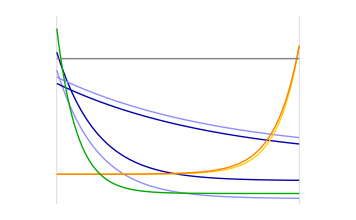

```mathematica
Plot[{Exp[-6x]-0.19,Exp[-6x]-0.05,Exp[-1.5x-0.5]+0.1,Exp[-1.5x-0.5]+0.15,Exp[11(x-1)],Exp[10(x-1)],Exp[-12x+0.25]-0.15,0.9},{x,0,1},PlotRange->{{-0.1,1.1},{-0.2,1.2}},Axes->False,GridLines->{{0,1},None},PlotStyle->{Directive[VNLight[Blue,2],Thick],Directive[VNDark[Blue,1],Thick],Directive[VNDark[Blue,1],Thick],Directive[VNLight[Blue,2],Thick],Directive[golden,Thick],Directive[Orange,Thick],Directive[VNDark[Green,1],Thick],Directive[Gray,Thick]}]
```

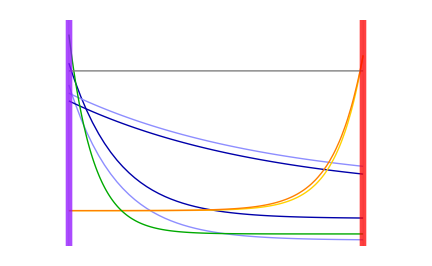
```mathematica
XDFig=-Graphics-;

epilogs={
Inset[Rotate[Text[MaTeX["\\mathbb{Z}_2 \\text{ bulk}",Magnification->LabelMag]],0Degree],Scaled[{0.5,0.95}]],
Inset[Rotate[Text[MaTeX["{\\color[rgb]"<>ToString[{0.35,0.35,0.35}]<>"\\text{SU}(3)^{(\\prime)} \\otimes \\text{SU}(2)^{(\\prime)} \\otimes \\text{U}(1)^{(\\prime)}}",Magnification->LegendMag]],0Degree],Scaled[{0.5,0.73}]],
Inset[Rotate[MaTeX["{\\color[rgb]"<>ToString[(List@@VNDark[Magenta,2])//N]<>"\\slashed{\\mathbb{Z}}_2 \\text{ boundary}}",Magnification->LabelMag],90Degree],Scaled[{0.04,0.75}]],
Inset[Rotate[MaTeX["{\\color[rgb]"<>ToString[(List@@VNDark[Red,1])//N]<>"\\mathbb{Z}_2 \\text{ boundary}}",Magnification->LabelMag],-90Degree],Scaled[{0.96,0.75}]],
Inset[Rotate[Text[MaTeX["{\\color[rgb]"<>ToString[(List@@VNLight[Blue,2])//N]<>" \\text{visible light fermions}}",Magnification->LegendMag]],0Degree],Scaled[{0.59,0.52}]],
Inset[Rotate[Text[MaTeX["{\\color[rgb]"<>ToString[(List@@VNDark[Blue,1])//N]<>" \\text{dark light fermions}}",Magnification->LegendMag]],0Degree],Scaled[{0.38,0.38}]],
Inset[Rotate[Text[MaTeX["{\\color[rgb]"<>ToString[(List@@Orange)//N]<>" t^{\\prime}}",Magnification->LegendMag]],0Degree],Scaled[{0.855,0.55}]],
Inset[Rotate[Text[MaTeX["{\\color[rgb]"<>ToString[(List@@golden)//N]<>" t}",Magnification->LegendMag]],0Degree],Scaled[{0.89,0.55}]],
Inset[Rotate[Text[MaTeX["{\\color[rgb]"<>ToString[(List@@VNDark[Green,2])//N]<>"R}",Magnification->LegendMag]],0Degree],Scaled[{0.15,0.25}]],
Inset[Rotate[Text[MaTeX["{\\color[rgb]"<>ToString[(List@@VNDark[Red,1])//N]<>"H^{(\\prime)}}",Magnification->LegendMag]],0Degree],Scaled[{0.96,0.4}]],
Inset[Rotate[Text[MaTeX["{\\color[rgb]"<>ToString[(List@@VNDark[Red,1])//N]<>"S^{(\\prime)}}",Magnification->LegendMag]],0Degree],Scaled[{0.96,0.32}]],
Inset[Rotate[Text[MaTeX["{\\color[rgb]"<>ToString[(List@@VNDark[Red,1])//N]<>"\\chi^{(\\prime)}}",Magnification->LegendMag]],0Degree],Scaled[{0.96,0.24}]],
Inset[Rotate[Text[MaTeX["{\\color[rgb]"<>ToString[(List@@VNDark[Red,1])//N]<>"\\psi^{(\\prime)}}",Magnification->LegendMag]],0Degree],Scaled[{0.96,0.16}]],
Inset[Rotate[Text[MaTeX["{\\color[rgb]"<>ToString[(List@@VNDark[Red,1])//N]<>"\\phi^{(\\prime)}}",Magnification->LegendMag]],0Degree],Scaled[{0.96,0.08}]]
};

Show[XDFig,Epilog->epilogs]
Export[PlotsDir<>"orbifold.pdf",%]

Clear[XDFig,epilogs]
```

-Graphics-

/home/buenabad/Dropbox/Projects/Active/a_baryon_dm_coincidence/mathematica files/../plots/orbifold.pdf

### Original

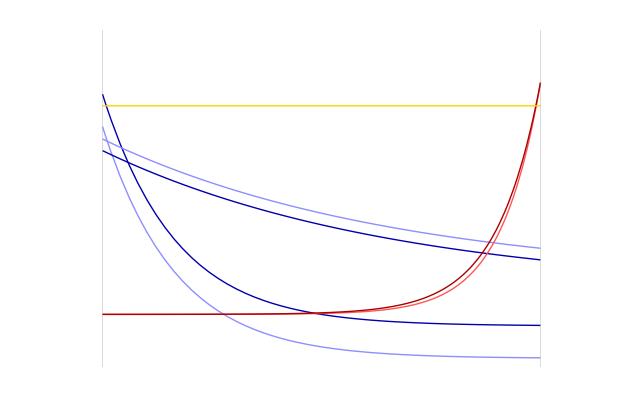

```mathematica
(*Plot[{Exp[-6x]-0.19,Exp[-6x]-0.05,Exp[-1.5x-0.5]+0.1,Exp[-1.5x-0.5]+0.15,Exp[11(x-1)],Exp[10(x-1)],0.9},{x,0,1},PlotRange->{{-0.1,1.1},{-0.2,1.2}},Axes->False,GridLines->{{0,1},None},PlotStyle->{Directive[VNLight[Blue,2],Thick],Directive[VNDark[Blue,1],Thick],Directive[VNDark[Blue,1],Thick],Directive[VNLight[Blue,2],Thick],Directive[VNLight[Red,1],Thick],Directive[VNDark[Red,1],Thick],Directive[golden,Thick]}]*)
```

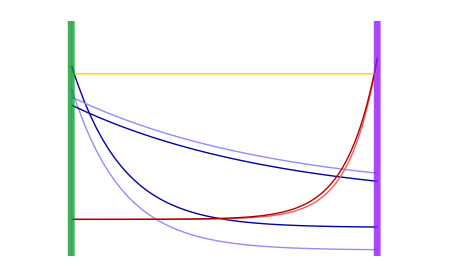
```mathematica
(*XDFig=-Graphics-;

epilogs={
Inset[Rotate[Text[MaTeX["\\mathbb{Z}_2 \\text{ bulk}",Magnification->LabelMag]],0Degree],Scaled[{0.5,0.95}]],
Inset[Rotate[Text[MaTeX["{\\color[rgb]"<>ToString[(List@@Orange)//N]<>"\\text{SU}(3)^{(\\prime)} \\otimes \\text{SU}(2)^{(\\prime)} \\otimes \\text{U}(1)^{(\\prime)}}",Magnification->LegendMag]],0Degree],Scaled[{0.5,0.73}]],
Inset[Rotate[MaTeX["{\\color[rgb]"<>ToString[(List@@VNDark[Green,2])//N]<>"\\slashed{\\mathbb{Z}}_2 \\text{ boundary}}",Magnification->LabelMag],90Degree],Scaled[{0.04,0.75}]],
Inset[Rotate[MaTeX["{\\color[rgb]"<>ToString[(List@@VNDark[Magenta,2])//N]<>"\\mathbb{Z}_2 \\text{ boundary}}",Magnification->LabelMag],-90Degree],Scaled[{0.97,0.75}]],
Inset[Rotate[Text[MaTeX["{\\color[rgb]"<>ToString[(List@@(*VNLight[Blue,1]*)Blue)//N]<>" \\text{light fermions}}",Magnification->LegendMag]],0Degree],Scaled[{0.55,0.52}]],
Inset[Rotate[Text[MaTeX["{\\color[rgb]"<>ToString[(List@@VNDark[Blue,1])//N]<>" \\text{dark light fermions}}",Magnification->LegendMag]],0Degree],Scaled[{0.4,0.38}]],
Inset[Rotate[Text[MaTeX["{\\color[rgb]"<>ToString[(List@@VNDark[Red,1])//N]<>" t^{\\prime}}",Magnification->LegendMag]],0Degree],Scaled[{0.855,0.55}]],
Inset[Rotate[Text[MaTeX["{\\color[rgb]"<>ToString[(List@@Red)//N]<>" t}",Magnification->LegendMag]],0Degree],Scaled[{0.89,0.55}]],
Inset[Rotate[Text[MaTeX["{\\color[rgb]"<>ToString[(List@@VNDark[Magenta,2])//N]<>"R}",Magnification->LegendMag]],0Degree],Scaled[{0.96,0.44}]],
Inset[Rotate[Text[MaTeX["{\\color[rgb]"<>ToString[(List@@VNDark[Magenta,2])//N]<>"H^{(\\prime)}}",Magnification->LegendMag]],0Degree],Scaled[{0.96,0.36}]],
Inset[Rotate[Text[MaTeX["{\\color[rgb]"<>ToString[(List@@VNDark[Magenta,2])//N]<>"S^{(\\prime)}}",Magnification->LegendMag]],0Degree],Scaled[{0.96,0.28}]],
Inset[Rotate[Text[MaTeX["{\\color[rgb]"<>ToString[(List@@VNDark[Magenta,2])//N]<>"\\chi^{(\\prime)}}",Magnification->LegendMag]],0Degree],Scaled[{0.96,0.2}]],
Inset[Rotate[Text[MaTeX["{\\color[rgb]"<>ToString[(List@@VNDark[Magenta,2])//N]<>"\\psi^{(\\prime)}}",Magnification->LegendMag]],0Degree],Scaled[{0.96,0.12}]],
Inset[Rotate[Text[MaTeX["{\\color[rgb]"<>ToString[(List@@VNDark[Magenta,2])//N]<>"\\phi^{(\\prime)}}",Magnification->LegendMag]],0Degree],Scaled[{0.96,0.04}]]
};

Show[XDFig,Epilog->epilogs]
Export[PlotsDir<>"orbifold.pdf",%]

Clear[XDFig,epilogs]

*)
```

-Graphics-

/home/buenabad/Dropbox/Projects/Active/a_baryon_dm_coincidence/mathematica files/../plots/orbifold.pdf

## Sketch: Thermal History

```mathematica
(*Plot[-10,{x,0,1},PlotRange->{0,1},Axes->False,PlotStyle->White]*)
```

```mathematica
ThHisFig=-Graphics-;
epilogs1={
Inset[MaTeX["T, \\ T^\\prime",Magnification->LabelMag],Scaled[{0.15,0.9}]],
Inset[MaTeX["t",Magnification->LabelMag],Scaled[{0.1,0.07}]],
Inset[Rotate[Text[MaTeX["{\\color{blue} T^\\prime = T}",Magnification->LegendMag]],90Degree],Scaled[{0.12,0.77}]],
Inset[Rotate[Text[MaTeX["{\\color{red} T^\\prime < T}",Magnification->LegendMag]],90Degree],Scaled[{0.12,0.23}]]
};

epilogs2={
Inset[MaTeX["{\\color{blue} \\text{VS \\& DS thermal bath}\\ (T > \\mathcal{O}(10~\\mathrm{TeV}))}",Magnification->1],Scaled[{0.5,0.8}]],
Inset[MaTeX["{\\color{blue} \\chi^{(\\prime)} \\text{ freeze-out}\\ (T \\lesssim m_{\\chi^{(\\prime)}}/\\mathcal{O}(10))}",Magnification->1],Scaled[{0.43,0.7}]],
Inset[MaTeX["{\\color[rgb]"<>ToString[List@@VNDark[Magenta,1]//N]<>" \\text{(Dark) Baryogenesis}\\ (\\chi^{(\\prime)}-\\text{decays})}",Magnification->1],Scaled[{0.46,0.6}]],
Inset[MaTeX["{\\color[rgb]"<>ToString[List@@VNDark[Magenta,1]//N]<>" \\text{Asymmetric Reheating}\\ (R-\\text{decays})}",Magnification->1],Scaled[{0.47,0.5}]],
Inset[MaTeX["{\\color[rgb]"<>ToString[List@@VNDark[Magenta,1]//N]<>" \\text{(Dark) Confinement}\\ (T^\\prime \\sim \\Lambda_{\\rm QCD}^{\\prime} > T \\sim \\Lambda_{\\rm QCD})}",Magnification->1],Scaled[{0.54,0.4}]],
Inset[MaTeX["{\\color{red} \\text{Dark symmetric annih.} \\ (T^\\prime \\sim \\text{few GeV -- few MeV})}",Magnification->1],Scaled[{0.57,0.3}]],
Inset[MaTeX["{\\color{red} \\nu^{(\\prime)} \\text{-decoupling \\& BBN (no dark BBN)} \\ (T \\sim \\mathrm{MeV})}",Magnification->1],Scaled[{0.57,0.2}]]
};

Show[ThHisFig,Epilog->epilogs1~Join~epilogs2,AspectRatio->1]

Export[PlotsDir<>"thermal_history.pdf",%]

Clear[ThHisFig,epilogs1,epilogs2]
```

-Graphics-

/home/buenabad/Dropbox/Projects/Active/a_baryon_dm_coincidence/mathematica files/../plots/thermal_history.pdf

## Scratch